## Set parameters

```mathematica
(*GRAVOTHERMAL SIMULATION*)
beta = 0.5; (*You have to put this by yourself in right place!!!*)

(*VALUES OF PARAMETERS*)
MassInit = Log10[1*10^9.89]; (*initial mass of the halo [10^x Solar Mass]*)
crossSection = 5.0; (*annihilation cross section[cm^2/g]*)
NumberOfRadi = 400; (*number of radi in the range of 10^-2 r_s, 10^2 r_s*)

(*SET THE TIME OF EVOLUTION*)
timeBeg = 0.; (*time, where [time] = GeV^-1]*)
(*IN GENERAL IT HAVE TO BE: timeBeg = 10^timeTxt[[1]];*)

(*timeEnd = 10^(-3.98108); (*early time, where [time] = GeV^-1]*)*)
timeEnd = 272; (*late time, where [time] = GeV^-1]*)
(*timeEnd = 2.5*880.17; (*time, where [time] = GeV^-1]*)*)
log10timeEnd =  Log10[timeEnd]; (*log10(time) where [time] = GeV^-1]*)

(*PRINTING TO MAKE SURE*)
Print["NumberOfRadi: ",NumberOfRadi]
Print["MassInit: ", MassInit]
Print["crossSection: ", crossSection]
Print["Ending time of simulation: ", timeEnd, " Gyr"]
Print["Begining time of simulation: ", timeBeg, " Gyr"]
```

NumberOfRadi: 400

MassInit: 9.89

crossSection: 5.

Ending time of simulation: 272 Gyr

Begining time of simulation: 0. Gyr

## Stuffs

```mathematica
<<MaTeX`
Needs["NumericalCalculus`"]
(*Needs["DifferentialEquations`NDSolveProblems`"];*)
(*Needs["DifferentialEquations`NDSolveUtilities`"];*)
ticks=Flatten[Join[Table[Join[{{10^j,StringForm["10^(``)",j],{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

ticksNoLabel=Flatten[Join[Table[Join[{{10^j,"",{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

ticksEven=Flatten[Join[Table[Join[{{10^j,If[Mod[j,2]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

ticksOdd=Flatten[Join[Table[Join[{{10^j,If[Mod[j,2]==1,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i*10^j,""},{i,2,9}]],{j,-200,10}]],1];

Logticks=Flatten[Join[Table[Join[{{Log[10,10^j],StringForm["10^(``)",j],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-30,10}]],1];

LogticksNoLabel=Flatten[Join[Table[Join[{{Log[10,10^j],"",{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,10}]],1];

LogticksEven=Flatten[Join[Table[Join[{{Log[10,10^j],If[Mod[j,2]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,10}]],1];

Logticks3=Flatten[Join[Table[Join[{{Log[10,10^j],If[Mod[j,3]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{Log[10,i*10^j],""},{i,2,9}]],{j,-20,10}]],1];

GridPointPlot[{u->if_InterpolatingFunction},t_,opts___]:=Module[{grid=InterpolatingFunctionCoordinates[if][[1]]},ListPlot[Transpose[{grid,if[grid,t]}],opts]]
```

## Compile functions (must evaluate this section before evaluating anything.)

```mathematica
hydroeq=Compile[{{ρ,_Real,1},{r,_Real,1},{σ,_Real,1},{M,_Real,1},{tG,_Real},{t0,_Real}},Module[{n=Length@ρ,inv=ρ,ϕ=ρ,ψ=ρ,aϕ=ρ,bϕ=ρ,cϕ=ρ,dϕ=ρ,aψ=ρ,bψ=ρ,cψ=ρ,dψ=ρ,α=ρ,γ=ρ,δr=ρ,δρ=ρ,nρ=ρ,nσ=σ,nr=r},
Do[
Do[inv[[j]]=(nσ[[j]])^3/nρ[[j]],{j,1,n}];
Do[ϕ[[j]]=(nρ[[j]]^(5/3) inv[[j]]^(2/3)-nρ[[j-1]]^(5/3) inv[[j-1]]^(2/3))/(M[[j]]-M[[j-1]])+((t0/tG)^2 (M[[j]]+M[[j-1]]))/(2 π^2 (nr[[j]]+nr[[j-1]])^4),{j,2,n}];
Do[ψ[[j]]=(M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])-1/2 π (nr[[j]]+nr[[j-1]])^2 (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
(**)
Do[aϕ[[j]]=-((2 (t0/tG)^2 (M[[j]]+M[[j-1]]))/(π^2 (nr[[j]]+nr[[j-1]])^5)),{j,2,n}];
Do[bϕ[[j]]=-((5 (nρ[[j-1]]^(2/3) inv[[j-1]]^(2/3)))/(3 (M[[j]]-M[[j-1]]))),{j,2,n}];
Do[cϕ[[j]]=-((2 (t0/tG)^2 (M[[j]]+M[[j-1]]))/(π^2 (nr[[j]]+nr[[j-1]])^5)),{j,2,n}];
Do[dϕ[[j]]=(5 (nρ[[j]]^(2/3) inv[[j]]^(2/3)))/(3 (M[[j]]-M[[j-1]])),{j,2,n}];
Do[aψ[[j]]=(M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])^2-π (nr[[j]]+nr[[j-1]]) (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
Do[bψ[[j]]=1/2 (-π) (nr[[j]]+nr[[j-1]])^2,{j,2,n}];
Do[cψ[[j]]=-((M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])^2)-π (nr[[j]]+nr[[j-1]]) (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
Do[dψ[[j]]=1/2 (-π) (nr[[j]]+nr[[j-1]])^2,{j,2,n}];
(**)
α[[1]]=0;
Do[α[[j]]=(dϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-dψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]]))/(cϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-cψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]])),{j,2,n}];
γ[[1]]=0;
Do[γ[[j]]=((bψ[[j]]-aψ[[j]] α[[j-1]]) (ϕ[[j]]-aϕ[[j]] γ[[j-1]])-(bϕ[[j]]-aϕ[[j]] α[[j-1]]) (ψ[[j]]-aψ[[j]] γ[[j-1]]))/(cϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-cψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]])),{j,2,n}];
(**)
δρ[[n]]=0;
δr[[n]]=-γ[[n]];
Do[δρ[[n-j]]=-((ψ[[n-j+1]]-aψ[[n-j+1]] γ[[n-j]]+cψ[[n-j+1]] δr[[n-j+1]]+dψ[[n-j+1]] δρ[[n-j+1]])/(bψ[[n-j+1]]-aψ[[n-j+1]] α[[n-j]]));
δr[[n-j]]=-γ[[n-j]]-α[[n-j]]*δρ[[n-j]];,{j,1,n-1}];
(**)
If[Max[Table[Abs[δr[[j]]/r[[j]]],{j,1,n}]]<10^-4.(*corvergence criterion*),Break[]];
Do[nr[[j]]=nr[[j]]+δr[[j]],{j,1,n}];
Do[nρ[[j]]=nρ[[j]]+δρ[[j]],{j,1,n}];
Do[nσ[[j]]=(nρ[[j]]*inv[[j]])^(1/3),{j,1,n}];
,{k,0,10^10}];
(**)
{nr,nρ,nσ}
]
,CompilationTarget->"C",RuntimeOptions->"Speed"];
(**)
heat=Compile[{{ρ,_Real,1},{r,_Real,1},{σ,_Real,1},{M,_Real,1},{ξ,_Real,1},{tG,_Real},{t0,_Real},{m,_Real},{r0,_Real},{ρ0,_Real}},
Module[{n=Length@ρ,nρ=ρ,nσ=σ,nr=r,nξ=ξ,κ=r,L=r,δucond=r,δusemi=r,δu=r,δT=r},
Do[κ[[j]]=((nσ[[j]]*(3/2 *(25(π)^(1/2))/32))^-1+(((2.18428*10^-6*m*t0)/(r0*nξ[[j]]*ρ0))/tG)^2*(3/2* 0.69*(16/π)^(1/2)* (nρ[[j]]*nσ[[j]]^3))^-1)^-1,{j,1,n}];
L[[1]]=0;
Do[L[[j]]=((2.18428*10^-6*m*t0)/(r0*nξ[[j]]*ρ0)(*tel*))/t0*4 π nr[[j]]^2*κ[[j]]*Piecewise[{{(nσ[[j+1]]^2-nσ[[j-1]]^2)/(nr[[j+1]]-nr[[j-1]]),1<j<n},{(-nσ[[j+2]]^2+4 nσ[[j+1]]^2-3 nσ[[j]]^2)/(nr[[j+2]]-nr[[j]]),j==1},{(3 nσ[[j]]^2-4 nσ[[j-1]]^2+nσ[[j-2]]^2)/(nr[[j]]-nr[[j-2]]),j==n}}],{j,2,n}];
Do[δucond[[j]]=Piecewise[{{(L[[j+1]]-L[[j-1]])/(M[[j+1]]-M[[j-1]]),1<j<n},{(-L[[j+2]]+4 L[[j+1]]-3 L[[j]])/(M[[j+2]]-M[[j]]),j==1},{(3 L[[j]]-4 L[[j-1]]+L[[j-2]])/(M[[j]]-M[[j-2]]),j==n}}],{j,1,n}];
Do[δu[[j]]=(δucond[[j]])/(3/2 nσ[[j]]^2),{j,1,n}];
δT[[1]]=(Max[Table[Abs[δu[[j]]],{j,1,n}]])^-1*10^-4.(*determination of the next time step*);
Do[nσ[[j]]=(Sqrt[2/3*((3/2 nσ[[j]]^2)+(δucond[[j]])*δT[[1]])]),{j,1,n}];
{δT,nσ}
]
,CompilationTarget->"C",RuntimeOptions->"Speed"];
(**)
(*concentration-mass relation*)
ρc=1.8791*(h^2)*1.4771*10^-7(*Solar Mass/(pc)^3*);
h=0.671;
a[z_]:=0.520+(0.905-0.520)*Exp[-0.617*z^1.21];
b[z_]:=-0.101+0.026*z;
c[M_,z_]:=10^a[z]*(M/((10^12)*(h^-1)(*Solar Mass*)))^b[z]*(13.3199/13.3199)(*5.26*(M/10^14)^-0.1*);
r0[M_,z_]:=(200*4/3 π*ρc)^(-1/3)*M^(1/3)*(c[M,z])^-1*10^-3(*in kpc*);
ρ0[M_,z_]:=M/(4 π*(r0[M,z]*10^3)^3) (1/(-(c[M,z]/(1+c[M,z]))+Log[1+c[M,z]]))(*ρc/3*c[M,z]^3*(-(c[M,z]/(1+c[M,z]))+Log[1+c[M,z]])^-1*)(*in Solar Mass/pc^3*);
z=0;
Mi=MassInit;(*match the range in "Evolution"*)
Mf=10.9;
NM=1;
δM=(Mf-Mi)/NM;
Do[M200[i]=10^(Mi+δM*i),{i,0,NM}];
Do[RS[i]=r0[M200[i],0],{i,0,NM}]
Do[DS[i]=ρ0[M200[i],0],{i,0,NM}]
Table[M200[i],{i,0,NM}]
Table[RS[i],{i,0,NM}]
Table[DS[i],{i,0,NM}]
Clear[Mi,Mf,NM,r0,ρ0,z,a,b,c,h,ρc,M];
```

{7.76247×10^9,7.94328×10^10}

{3.07431,8.44159}

{0.0121228,0.00676539}

## Cross section tabulation: example) Resonant SIDM

```mathematica
σmresonantNv[σm0_,m_,L_,γ_,vR_,ν_(*1d-velocity dispersion*)]:=σm0+(256π)/m^2*1/m*(NIntegrate[(v^(4 L+1) γ^2)/((v^2-vR^2)^2+16 v^(2+4 L) γ^2)*((4π*v^2*Exp[-v^2/(4*(ν)^2)])/((4π*(ν)^2)^(3/2))),{v,0,(1-Abs[10*(2 (2 (1+2 L) vR^(2+4 L) γ^2+√(vR^(6+4 L) γ^2-8 L (1+2 L) vR^(4+8 L) γ^4)))/(vR^4-4 (1+6 L+8 L^2) vR^(2+4 L) γ^2)])*vR}]+ NIntegrate[(v^(4 L+1)  γ^2)/((v^2-vR^2)^2+16 v^(2+4 L) γ^2)*((4π*v^2*Exp[-v^2/(4*(ν)^2)])/((4π*(ν)^2)^(3/2))),{v,(1-Abs[10*(2 (2 (1+2 L) vR^(2+4 L) γ^2+√(vR^(6+4 L) γ^2-8 L (1+2 L) vR^(4+8 L) γ^4)))/(vR^4-4 (1+6 L+8 L^2) vR^(2+4 L) γ^2)])*vR,(1+Abs[10*(2 (2 (1+2 L) vR^(2+4 L) γ^2+√(vR^(6+4 L) γ^2-8 L (1+2 L) vR^(4+8 L) γ^4)))/(vR^4-4 (1+6 L+8 L^2) vR^(2+4 L) γ^2)])*vR}]+ NIntegrate[(v^(4 L+1)  γ^2)/((v^2-vR^2)^2+16 v^(2+4 L) γ^2)*((4π*v^2*Exp[-v^2/(4*(ν)^2)])/((4π*(ν)^2)^(3/2))),{v,(1+Abs[10*(2 (2 (1+2 L) vR^(2+4 L) γ^2+√(vR^(6+4 L) γ^2-8 L (1+2 L) vR^(4+8 L) γ^4)))/(vR^4-4 (1+6 L+8 L^2) vR^(2+4 L) γ^2)])*vR,Infinity}])/(4578.17)/(4/(π)^(1/2)ν);
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00036}. NIntegrate obtained 2.49694×10^-303 and 3.84179×10^-309 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.000360021}. NIntegrate obtained 1.36301×10^-7 and 1.38773×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.000360021}. NIntegrate obtained 1.34067×10^-7 and 1.37053×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

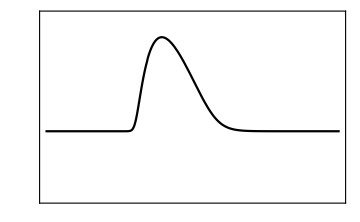

```mathematica
vf=Log10[10^4/(3*10^5)];
vi=Log10[0.01/(3*10^5)];
Nv=2400;
δv=(vf-vi)/Nv;
σm0=0.03;
vR=108./(3*10^5);
γ=10^-3.;
mtilde=0.4(*GeV*);
L=1;
datav=Table[{vi+δv*i,Log10[σmresonantNv[σm0,mtilde,L,γ,vR,10^(vi+δv*i)(*1d-velocity dispersion*)]]},{i,0,Nv}];
σmRSIDMint=Interpolation[datav,InterpolationOrder->1];Plot[{σmRSIDMint[v-Log10[(3*10^5)]]},{v,Log10[1.],Log10[10^4.]},PlotRange->{-3.,1},Frame->True,FrameLabel->{MaTeX["\\nu \\,\\left[{\\rm km/s}\\right]",Magnification->1.7],MaTeX["\\langle\\sigma_{\\rm self}v_{\\rm rel} \\rangle/\\langle v_{\\rm rel} \\rangle m \\,\\left[ {\\rm cm^2/g} \\right]",Magnification->1.5]},FrameTicks->{{Logticks,LogticksNoLabel},{Logticks,LogticksNoLabel}},FrameTicksStyle->Directive[Black,15],PlotStyle->{{Black}},Axes->False,ImageSize->Medium,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Latin Modern Roman"},PlotRangePadding->None]
Clear[vf,vi,Nv,δv,σm0,vR,γ,mtilde,L,datav];
```

## Evolution

```mathematica
SetDirectory[NotebookDirectory[]];(*output directory*)
(**)
Mi=MassInit;(*to scan halo masses, change also "p" range below*)(*match the range in "Compile functions"*)
Mf=10.9;
NM=1;
δM=(Mf-Mi)/NM;
AbsoluteTiming[Do[(*mass loop*)
Print["M="<>ToString[Mi+δM*p]];
(*Set up initial r-grid in Log-bin*)
ri=-2.(*Log10[Subscript[r, i=1]/Subscript[r, 0]]*);(*-4 for rSIDM*)
rf=2.(*Log10[Subscript[r, i=NR]/Subscript[r, 0]]*);(*2 for rSIDM*)
NR=NumberOfRadi;(*700 for rSIDM*)
δR=(rf-ri)/NR;
(*NFW scale parameters for given halo mass*)
rs=RS[p](*in kpc*);
ρs=DS[p](*in Solarmass/pc^3*);
(**)
G=1/((1.220890 10^19)^2)(*GeV^-2*);
m=1(*GeV*)(*dummy variable: do not change this!*);
r0=rs*1.56 10^35(*in GeV^-1,1 kpc*);
t0=4.79 10^40(*in GeV^-1*)(*1 Gyr*);
ρ0=(ρs)*2.94*10^-40(*Gev^4,Solarmass/pc^3*);(*Subscript[σ, 0] = Subscript[r, 0]/Subscript[t, 0]*)
tG=√(1/(4 π G ρ0));
(**)
t=0.;
Tticker=0;
ticker=1;
(*set r-grid*)
r[0]=0;
Do[r[j]=10^(ri+δR*(j-1)),{j,1,NR+1}];
Table[r[j],{j,0,NR+1}];
(*initial ρ-grid*)
ρ[0]=NIntegrate[(4π*x^2)/(x*(1+x)^2),{x,0,10^ri}]*(4/3 π*10^(3*ri))^-1;(*assumed NFW*)
Do[ρ[j]=1/((10^(ri+δR*(j-1)))*(1+10^(ri+δR*(j-1)))^2),{j,1,NR+1}];
Table[ρ[j],{j,0,NR+1}];
(*initial M-grid*)
M[0]=0;
M[1]=NIntegrate[(4π*x^2)/(x*(1+x)^2),{x,0,10^ri}];(*assumed NFW*)
Do[M[j]=M[j-1]+π/2*(r[j]+r[j-1])^2*(ρ[j]+ρ[j-1])*(r[j]-r[j-1]),{j,2,NR+1}];
Table[M[j],{j,0,NR+1}];
(*initial σ-grid*)
ρσ[NR+1]=ρ[NR+1]*(16.9195*(2*ρs)^(1/2))^2;(*precisely ρσ^2*)(*arbitrary as long as numerically stable*)
Do[ρσ[(NR+1)-j]=ρσ[(NR+1)-j+1]+(t0/tG)^2*(((M[(NR+1)-j]+M[(NR+1)-j+1])*(ρ[(NR+1)-j]+ρ[(NR+1)-j+1]))/(4π*(r[(NR+1)-j]+r[(NR+1)-j+1])^2))*(r[(NR+1)-j+1]-r[(NR+1)-j]),{j,1,NR+1}];
Do[σ[j]=√(ρσ[j]/ρ[j]),{j,0,NR+1}];
Table[σ[j],{j,0,NR+1}];
Table[{r[j],σ[j]},{j,0,NR+1}];
ListLogPlot[Table[{r[j],σ[j]},{j,0,NR+1}]];
(**)
ρarray=Table[ρ[j],{j,0,NR+1}];
rarray=Table[r[j],{j,0,NR+1}];
σharray=Table[σ[j],{j,0,NR+1}](*not σarray!*);
Marray=Table[M[j],{j,0,NR+1}];
Clear[ρ,r,σ];
(**)
neweq=hydroeq[ρarray,rarray,σharray,Marray,tG,t0];
rarray=neweq[[1]];
ρarray=neweq[[2]];
σarray=neweq[[3]];

Do[(*time loop*)
(*Update SIDM cross section distribution with respect to the new equilibrium profile*)
ξarray=Table[(*ξ=*)(crossSection(*10^σmRSIDMint[Log10[σarray[[j]]*r0/t0]]*))/(1(*cm^2/g*))*0.01,{j,1,NR+2}];(*velocity dependence taken into account*)
(*Heat velocity dispersion.*)
h=heat[ρarray,rarray,σarray,Marray,ξarray,tG,(*tJ,*)t0,m,r0,ρ0];
δT=h[[1]][[1]](*time evolution step*);
σharray=h[[2]](*heated velocity dispersion*);
t=t+δT;
(*Find new hydrostatic equilibrium.*)
neweq=hydroeq[ρarray,rarray,σharray,Marray,tG,t0];
rarray=neweq[[1]];
ρarray=neweq[[2]];
σarray=neweq[[3]];
(*Record solution for the specified time slice, and print Kn*)
If[
Log10[t]≥-4.(*initial time when you wish to start recording, Log10[Subscript[t, i]/t0]*)+0.0025(*time resolution that you wish to record*)*Tticker∧ticker==1,
Do[ρsol[Tticker][j]=ρarray[[j+1]],{j,0,NR+1}];
Do[rsol[Tticker][j]=rarray[[j+1]],{j,0,NR+1}];
Do[σsol[Tticker][j]=σarray[[j+1]],{j,0,NR+1}];
T[Tticker]=Log10[t];
Kn=√(4 π G ρarray[[1]]*ρ0)*1/(ρarray[[1]]*(ξarray[[1]]/0.01*4578.17)*σarray[[1]])*1/((r0 ρ0)/t0);
Print["Solved for t="<>ToString[T[Tticker]]<>", Kn="<>ToString[Kn]];
Tticker=Tticker+1;
ticker=0;,
ticker=1;
];
If[(*ρarray[[1]]>101.*)Log10[t]>Log10[timeEnd],(*condition to finish computation*)
Do[ρsol[Tticker][j]=ρarray[[j+1]],{j,0,NR+1}];
Do[rsol[Ttiscker][j]=rarray[[j+1]],{j,0,NR+1}];
Do[σsol[Tticker][j]=σarray[[j+1]],{j,0,NR+1}];
T[Tticker]=Log10[t];
Kn=√(4 π G ρarray⟦1⟧ ρ0)*1/(ρarray⟦1⟧*(ξarray[[1]]/0.01*4578.17)* σarray⟦1⟧)*1/((r0 ρ0)/t0);
Print["Solved for t="<>ToString[T[Tticker]]<>", Kn="<>ToString[Kn]];
Break[];
];
Clear[δT];
,{i,0,10^10}];
Print["Exporting data..."];
datasolfinal=Flatten[Table[{T[i],rsol[i][j],ρsol[i][j], σsol[i][j]},{i,0,Tticker},{j,0,NR+1}],1];
Export["ρσ_sol_M_"<>ToString[Mi+δM*p]<> "_t_" <> 
    TextString[timeEnd] <> "_sigma_" <> TextString[crossSection] <> "_beta_" <> TextString[beta]<>
    ".csv", datasolfinal, "Table"];
Print["Data export complete!"];
,{p,0,0}];](*change it to {p,0,NM}, to scan halo masses*)
Print["Job ended."]
```

M=9.89

Solved for t=-3.99922, Kn=16.8048

Solved for t=-3.99694, Kn=16.8052

Solved for t=-3.99467, Kn=16.8055

Solved for t=-3.9924, Kn=16.8059

Solved for t=-3.98917, Kn=16.7913

Solved for t=-3.98708, Kn=16.7916

Solved for t=-3.98499, Kn=16.792

Solved for t=-3.98186, Kn=16.7925

Solved for t=-3.97977, Kn=16.7929

Solved for t=-3.97663, Kn=16.7934

Solved for t=-3.97454, Kn=16.7938

Solved for t=-3.97246, Kn=16.7942

Solved for t=-3.96932, Kn=16.7947

Solved for t=-3.96724, Kn=16.7951

Solved for t=-3.96411, Kn=16.7956

Solved for t=-3.96202, Kn=16.796

Solved for t=-3.95994, Kn=16.7964

Solved for t=-3.95681, Kn=16.7969

Solved for t=-3.95473, Kn=16.7973

Solved for t=-3.9516, Kn=16.7979

Solved for t=-3.94952, Kn=16.7983

Solved for t=-3.94744, Kn=16.7986

Solved for t=-3.94432, Kn=16.7992

Solved for t=-3.94224, Kn=16.7996

Solved for t=-3.93913, Kn=16.8002

Solved for t=-3.93705, Kn=16.8006

Solved for t=-3.93497, Kn=16.801

Solved for t=-3.93186, Kn=16.8015

Solved for t=-3.92979, Kn=16.8019

Solved for t=-3.92668, Kn=16.8025

Solved for t=-3.92461, Kn=16.8029

Solved for t=-3.92151, Kn=16.8035

Solved for t=-3.91944, Kn=16.8039

Solved for t=-3.91737, Kn=16.8043

Solved for t=-3.91427, Kn=16.8049

Solved for t=-3.91228, Kn=16.7909

Solved for t=-3.90938, Kn=16.7915

Solved for t=-3.90745, Kn=16.7919

Solved for t=-3.90456, Kn=16.7924

Solved for t=-3.90167, Kn=16.793

Solved for t=-3.89974, Kn=16.7934

Solved for t=-3.89684, Kn=16.794

Solved for t=-3.89492, Kn=16.7944

Solved for t=-3.89202, Kn=16.795

Solved for t=-3.88913, Kn=16.7956

Solved for t=-3.88721, Kn=16.796

Solved for t=-3.88432, Kn=16.7966

Solved for t=-3.88239, Kn=16.797

Solved for t=-3.8795, Kn=16.7976

Solved for t=-3.87661, Kn=16.7982

Solved for t=-3.87469, Kn=16.7986

Solved for t=-3.8718, Kn=16.7992

Solved for t=-3.86988, Kn=16.7996

Solved for t=-3.867, Kn=16.8002

Solved for t=-3.86412, Kn=16.8009

Solved for t=-3.8622, Kn=16.8013

Solved for t=-3.85932, Kn=16.8019

Solved for t=-3.8574, Kn=16.8023

Solved for t=-3.85452, Kn=16.803

Solved for t=-3.85165, Kn=16.8036

Solved for t=-3.84973, Kn=16.804

Solved for t=-3.84691, Kn=16.7907

Solved for t=-3.8442, Kn=16.7913

Solved for t=-3.84239, Kn=16.7917

Solved for t=-3.83968, Kn=16.7924

Solved for t=-3.83697, Kn=16.793

Solved for t=-3.83425, Kn=16.7936

Solved for t=-3.83245, Kn=16.794

Solved for t=-3.82974, Kn=16.7947

Solved for t=-3.82702, Kn=16.7953

Solved for t=-3.82431, Kn=16.7959

Solved for t=-3.8216, Kn=16.7966

Solved for t=-3.8198, Kn=16.797

Solved for t=-3.81709, Kn=16.7976

Solved for t=-3.81438, Kn=16.7983

Solved for t=-3.81167, Kn=16.7989

Solved for t=-3.80987, Kn=16.7994

Solved for t=-3.80716, Kn=16.8

Solved for t=-3.80446, Kn=16.8007

Solved for t=-3.80175, Kn=16.8013

Solved for t=-3.79995, Kn=16.8018

Solved for t=-3.79725, Kn=16.8025

Solved for t=-3.79455, Kn=16.8031

Solved for t=-3.79185, Kn=16.7904

Solved for t=-3.78928, Kn=16.791

Solved for t=-3.78671, Kn=16.7917

Solved for t=-3.785, Kn=16.7921

Solved for t=-3.78243, Kn=16.7928

Solved for t=-3.77986, Kn=16.7934

Solved for t=-3.77729, Kn=16.7941

Solved for t=-3.77472, Kn=16.7948

Solved for t=-3.77215, Kn=16.7954

Solved for t=-3.76959, Kn=16.7961

Solved for t=-3.76702, Kn=16.7968

Solved for t=-3.76445, Kn=16.7974

Solved for t=-3.76188, Kn=16.7981

Solved for t=-3.75932, Kn=16.7988

Solved for t=-3.75675, Kn=16.7995

Solved for t=-3.75419, Kn=16.8002

Solved for t=-3.75248, Kn=16.8007

Solved for t=-3.74992, Kn=16.8013

Solved for t=-3.74735, Kn=16.802

Solved for t=-3.74479, Kn=16.8027

Solved for t=-3.74227, Kn=16.7905

Solved for t=-3.73981, Kn=16.7912

Solved for t=-3.73736, Kn=16.7919

Solved for t=-3.73491, Kn=16.7926

Solved for t=-3.73246, Kn=16.7933

Solved for t=-3.72918, Kn=16.7942

Solved for t=-3.72673, Kn=16.7949

Solved for t=-3.72428, Kn=16.7956

Solved for t=-3.72183, Kn=16.7963

Solved for t=-3.71938, Kn=16.797

Solved for t=-3.71692, Kn=16.7977

Solved for t=-3.71447, Kn=16.7984

Solved for t=-3.71202, Kn=16.7991

Solved for t=-3.70957, Kn=16.7998

Solved for t=-3.70713, Kn=16.8006

Solved for t=-3.70468, Kn=16.8013

Solved for t=-3.70223, Kn=16.802

Solved for t=-3.69978, Kn=16.7902

Solved for t=-3.69743, Kn=16.7909

Solved for t=-3.69429, Kn=16.7919

Solved for t=-3.69193, Kn=16.7926

Solved for t=-3.68958, Kn=16.7933

Solved for t=-3.68722, Kn=16.7941

Solved for t=-3.68487, Kn=16.7948

Solved for t=-3.68173, Kn=16.7958

Solved for t=-3.67937, Kn=16.7965

Solved for t=-3.67702, Kn=16.7972

Solved for t=-3.67467, Kn=16.798

Solved for t=-3.67231, Kn=16.7987

Solved for t=-3.66996, Kn=16.7994

Solved for t=-3.66682, Kn=16.8004

Solved for t=-3.66447, Kn=16.8012

Solved for t=-3.66212, Kn=16.8019

Solved for t=-3.65982, Kn=16.7907

Solved for t=-3.65679, Kn=16.7917

Solved for t=-3.65452, Kn=16.7924

Solved for t=-3.65225, Kn=16.7932

Solved for t=-3.64997, Kn=16.7939

Solved for t=-3.64694, Kn=16.7949

Solved for t=-3.64467, Kn=16.7957

Solved for t=-3.6424, Kn=16.7964

Solved for t=-3.63937, Kn=16.7975

Solved for t=-3.6371, Kn=16.7982

Solved for t=-3.63483, Kn=16.799

Solved for t=-3.6318, Kn=16.8

Solved for t=-3.62953, Kn=16.8008

Solved for t=-3.62726, Kn=16.8016

Solved for t=-3.62431, Kn=16.791

Solved for t=-3.62211, Kn=16.7918

Solved for t=-3.6199, Kn=16.7925

Solved for t=-3.61697, Kn=16.7935

Solved for t=-3.61477, Kn=16.7943

Solved for t=-3.61183, Kn=16.7954

Solved for t=-3.60963, Kn=16.7961

Solved for t=-3.60743, Kn=16.7969

Solved for t=-3.6045, Kn=16.798

Solved for t=-3.6023, Kn=16.7988

Solved for t=-3.59937, Kn=16.7998

Solved for t=-3.59717, Kn=16.8006

Solved for t=-3.59497, Kn=16.8014

Solved for t=-3.5921, Kn=16.7911

Solved for t=-3.58997, Kn=16.7918

Solved for t=-3.58712, Kn=16.7929

Solved for t=-3.58498, Kn=16.7937

Solved for t=-3.58213, Kn=16.7948

Solved for t=-3.57999, Kn=16.7956

Solved for t=-3.57715, Kn=16.7966

Solved for t=-3.5743, Kn=16.7977

Solved for t=-3.57216, Kn=16.7985

Solved for t=-3.56932, Kn=16.7996

Solved for t=-3.56718, Kn=16.8004

Solved for t=-3.56434, Kn=16.7903

Solved for t=-3.56226, Kn=16.7911

Solved for t=-3.55948, Kn=16.7922

Solved for t=-3.5574, Kn=16.793

Solved for t=-3.55463, Kn=16.7941

Solved for t=-3.55186, Kn=16.7952

Solved for t=-3.54978, Kn=16.796

Solved for t=-3.547, Kn=16.7971

Solved for t=-3.54493, Kn=16.798

Solved for t=-3.54216, Kn=16.7991

Solved for t=-3.53938, Kn=16.8002

Solved for t=-3.53731, Kn=16.801

Solved for t=-3.53459, Kn=16.7913

Solved for t=-3.53188, Kn=16.7924

Solved for t=-3.52985, Kn=16.7932

Solved for t=-3.52715, Kn=16.7943

Solved for t=-3.52444, Kn=16.7954

Solved for t=-3.52242, Kn=16.7963

Solved for t=-3.51971, Kn=16.7974

Solved for t=-3.51701, Kn=16.7986

Solved for t=-3.51498, Kn=16.7994

Solved for t=-3.51228, Kn=16.8005

Solved for t=-3.50961, Kn=16.7911

Solved for t=-3.50697, Kn=16.7923

Solved for t=-3.50498, Kn=16.7931

Solved for t=-3.50234, Kn=16.7942

Solved for t=-3.4997, Kn=16.7954

Solved for t=-3.49706, Kn=16.7965

Solved for t=-3.49441, Kn=16.7977

Solved for t=-3.49243, Kn=16.7986

Solved for t=-3.48979, Kn=16.7997

Solved for t=-3.48715, Kn=16.8009

Solved for t=-3.48455, Kn=16.7916

Solved for t=-3.48196, Kn=16.7927

Solved for t=-3.47938, Kn=16.7939

Solved for t=-3.47744, Kn=16.7948

Solved for t=-3.47485, Kn=16.7959

Solved for t=-3.47227, Kn=16.7971

Solved for t=-3.46968, Kn=16.7983

Solved for t=-3.4671, Kn=16.7995

Solved for t=-3.46451, Kn=16.8007

Solved for t=-3.46197, Kn=16.7918

Solved for t=-3.45943, Kn=16.7929

Solved for t=-3.4569, Kn=16.7941

Solved for t=-3.455, Kn=16.795

Solved for t=-3.45246, Kn=16.7962

Solved for t=-3.44993, Kn=16.7974

Solved for t=-3.4474, Kn=16.7986

Solved for t=-3.44486, Kn=16.7998

Solved for t=-3.44233, Kn=16.7911

Solved for t=-3.43984, Kn=16.7923

Solved for t=-3.43735, Kn=16.7935

Solved for t=-3.43487, Kn=16.7947

Solved for t=-3.43238, Kn=16.7959

Solved for t=-3.42989, Kn=16.7971

Solved for t=-3.42741, Kn=16.7983

Solved for t=-3.42492, Kn=16.7995

Solved for t=-3.42244, Kn=16.8008

Solved for t=-3.41998, Kn=16.7922

Solved for t=-3.41693, Kn=16.7937

Solved for t=-3.41449, Kn=16.7949

Solved for t=-3.41205, Kn=16.7962

Solved for t=-3.4096, Kn=16.7974

Solved for t=-3.40716, Kn=16.7987

Solved for t=-3.40472, Kn=16.7999

Solved for t=-3.40228, Kn=16.7915

Solved for t=-3.39988, Kn=16.7927

Solved for t=-3.39748, Kn=16.794

Solved for t=-3.39447, Kn=16.7955

Solved for t=-3.39207, Kn=16.7968

Solved for t=-3.38967, Kn=16.7981

Solved for t=-3.38727, Kn=16.7993

Solved for t=-3.38487, Kn=16.8006

Solved for t=-3.38249, Kn=16.7924

Solved for t=-3.37954, Kn=16.794

Solved for t=-3.37717, Kn=16.7952

Solved for t=-3.37481, Kn=16.7965

Solved for t=-3.37245, Kn=16.7978

Solved for t=-3.3695, Kn=16.7994

Solved for t=-3.36713, Kn=16.8006

Solved for t=-3.36479, Kn=16.7927

Solved for t=-3.36246, Kn=16.7939

Solved for t=-3.35955, Kn=16.7955

Solved for t=-3.35723, Kn=16.7968

Solved for t=-3.3549, Kn=16.7981

Solved for t=-3.35199, Kn=16.7997

Solved for t=-3.34967, Kn=16.801

Solved for t=-3.34737, Kn=16.7933

Solved for t=-3.3445, Kn=16.7949

Solved for t=-3.34221, Kn=16.7962

Solved for t=-3.33991, Kn=16.7975

Solved for t=-3.33705, Kn=16.7991

Solved for t=-3.33475, Kn=16.8005

Solved for t=-3.33247, Kn=16.793

Solved for t=-3.32964, Kn=16.7946

Solved for t=-3.32738, Kn=16.7959

Solved for t=-3.32455, Kn=16.7975

Solved for t=-3.32229, Kn=16.7989

Solved for t=-3.31946, Kn=16.8005

Solved for t=-3.31721, Kn=16.7933

Solved for t=-3.31497, Kn=16.7946

Solved for t=-3.31218, Kn=16.7963

Solved for t=-3.30995, Kn=16.7976

Solved for t=-3.30716, Kn=16.7993

Solved for t=-3.30493, Kn=16.8006

Solved for t=-3.30214, Kn=16.7936

Solved for t=-3.29994, Kn=16.795

Solved for t=-3.29718, Kn=16.7966

Solved for t=-3.29498, Kn=16.798

Solved for t=-3.29222, Kn=16.7997

Solved for t=-3.28947, Kn=16.8014

Solved for t=-3.28728, Kn=16.7943

Solved for t=-3.28456, Kn=16.796

Solved for t=-3.28238, Kn=16.7974

Solved for t=-3.27966, Kn=16.7991

Solved for t=-3.27748, Kn=16.8004

Solved for t=-3.27476, Kn=16.794

Solved for t=-3.27206, Kn=16.7957

Solved for t=-3.26991, Kn=16.7971

Solved for t=-3.26722, Kn=16.7988

Solved for t=-3.26453, Kn=16.8005

Solved for t=-3.26238, Kn=16.8019

Solved for t=-3.2597, Kn=16.7954

Solved for t=-3.25704, Kn=16.7972

Solved for t=-3.25491, Kn=16.7985

Solved for t=-3.25225, Kn=16.8003

Solved for t=-3.24959, Kn=16.802

Solved for t=-3.24747, Kn=16.7955

Solved for t=-3.24484, Kn=16.7972

Solved for t=-3.24221, Kn=16.799

Solved for t=-3.23957, Kn=16.8007

Solved for t=-3.23747, Kn=16.8021

Solved for t=-3.23485, Kn=16.7959

Solved for t=-3.23224, Kn=16.7977

Solved for t=-3.22964, Kn=16.7994

Solved for t=-3.22703, Kn=16.8012

Solved for t=-3.22495, Kn=16.8026

Solved for t=-3.22236, Kn=16.7967

Solved for t=-3.21978, Kn=16.7985

Solved for t=-3.2172, Kn=16.8002

Solved for t=-3.21462, Kn=16.802

Solved for t=-3.21204, Kn=16.7961

Solved for t=-3.20999, Kn=16.7975

Solved for t=-3.20744, Kn=16.7993

Solved for t=-3.20489, Kn=16.8011

Solved for t=-3.20233, Kn=16.8029

Solved for t=-3.19979, Kn=16.7973

Solved for t=-3.19725, Kn=16.7991

Solved for t=-3.19472, Kn=16.8008

Solved for t=-3.19219, Kn=16.8026

Solved for t=-3.18966, Kn=16.797

Solved for t=-3.18715, Kn=16.7988

Solved for t=-3.18465, Kn=16.8006

Solved for t=-3.18214, Kn=16.8024

Solved for t=-3.17963, Kn=16.8042

Solved for t=-3.17714, Kn=16.799

Solved for t=-3.17465, Kn=16.8008

Solved for t=-3.17217, Kn=16.8026

Solved for t=-3.16968, Kn=16.8044

Solved for t=-3.16721, Kn=16.7991

Solved for t=-3.16474, Kn=16.8009

Solved for t=-3.16228, Kn=16.8027

Solved for t=-3.15981, Kn=16.8046

Solved for t=-3.15735, Kn=16.7993

Solved for t=-3.15491, Kn=16.8011

Solved for t=-3.15247, Kn=16.8029

Solved for t=-3.14953, Kn=16.8051

Solved for t=-3.1471, Kn=16.8001

Solved for t=-3.14467, Kn=16.802

Solved for t=-3.14225, Kn=16.8038

Solved for t=-3.13982, Kn=16.8057

Solved for t=-3.13741, Kn=16.8007

Solved for t=-3.13452, Kn=16.8029

Solved for t=-3.13211, Kn=16.8048

Solved for t=-3.12971, Kn=16.8066

Solved for t=-3.12732, Kn=16.8016

Solved for t=-3.12493, Kn=16.8035

Solved for t=-3.12206, Kn=16.8057

Solved for t=-3.11968, Kn=16.8011

Solved for t=-3.11731, Kn=16.8029

Solved for t=-3.11494, Kn=16.8048

Solved for t=-3.1121, Kn=16.807

Solved for t=-3.10973, Kn=16.8024

Solved for t=-3.10738, Kn=16.8043

Solved for t=-3.10456, Kn=16.8065

Solved for t=-3.1022, Kn=16.8019

Solved for t=-3.09987, Kn=16.8037

Solved for t=-3.09706, Kn=16.806

Solved for t=-3.09473, Kn=16.8079

Solved for t=-3.0924, Kn=16.8036

Solved for t=-3.08962, Kn=16.8058

Solved for t=-3.08729, Kn=16.8077

Solved for t=-3.08498, Kn=16.8034

Solved for t=-3.08221, Kn=16.8057

Solved for t=-3.0799, Kn=16.8076

Solved for t=-3.07714, Kn=16.8037

Solved for t=-3.07485, Kn=16.8056

Solved for t=-3.0721, Kn=16.8078

Solved for t=-3.06981, Kn=16.8097

Solved for t=-3.06707, Kn=16.8058

Solved for t=-3.0648, Kn=16.8077

Solved for t=-3.06207, Kn=16.81

Solved for t=-3.0598, Kn=16.8061

Solved for t=-3.05709, Kn=16.8084

Solved for t=-3.05483, Kn=16.8103

Solved for t=-3.05212, Kn=16.8067

Solved for t=-3.04987, Kn=16.8086

Solved for t=-3.04717, Kn=16.8109

Solved for t=-3.04493, Kn=16.807

Solved for t=-3.04225, Kn=16.8093

Solved for t=-3.03957, Kn=16.8116

Solved for t=-3.03734, Kn=16.8077

Solved for t=-3.03468, Kn=16.81

Solved for t=-3.03246, Kn=16.8119

Solved for t=-3.0298, Kn=16.8084

Solved for t=-3.02715, Kn=16.8107

Solved for t=-3.02494, Kn=16.8126

Solved for t=-3.0223, Kn=16.8095

Solved for t=-3.01966, Kn=16.8118

Solved for t=-3.01747, Kn=16.8137

Solved for t=-3.01484, Kn=16.8106

Solved for t=-3.01222, Kn=16.8129

Solved for t=-3.0096, Kn=16.8098

Solved for t=-3.00743, Kn=16.8117

Solved for t=-3.00482, Kn=16.814

Solved for t=-3.00222, Kn=16.8109

Solved for t=-2.99963, Kn=16.8132

Solved for t=-2.99747, Kn=16.8151

Solved for t=-2.99488, Kn=16.812

Solved for t=-2.9923, Kn=16.8144

Solved for t=-2.98973, Kn=16.8167

Solved for t=-2.98716, Kn=16.8139

Solved for t=-2.98459, Kn=16.8162

Solved for t=-2.98246, Kn=16.8131

Solved for t=-2.97991, Kn=16.8155

Solved for t=-2.97735, Kn=16.8178

Solved for t=-2.97481, Kn=16.8151

Solved for t=-2.97227, Kn=16.8174

Solved for t=-2.96973, Kn=16.8147

Solved for t=-2.96721, Kn=16.817

Solved for t=-2.96468, Kn=16.8193

Solved for t=-2.96216, Kn=16.8166

Solved for t=-2.95965, Kn=16.819

Solved for t=-2.95714, Kn=16.8163

Solved for t=-2.95464, Kn=16.8186

Solved for t=-2.95214, Kn=16.8209

Solved for t=-2.94965, Kn=16.8186

Solved for t=-2.94716, Kn=16.821

Solved for t=-2.94468, Kn=16.8187

Solved for t=-2.9422, Kn=16.821

Solved for t=-2.93973, Kn=16.8187

Solved for t=-2.93727, Kn=16.821

Solved for t=-2.9348, Kn=16.8233

Solved for t=-2.93235, Kn=16.8211

Solved for t=-2.9299, Kn=16.8234

Solved for t=-2.92745, Kn=16.8212

Solved for t=-2.92461, Kn=16.8239

Solved for t=-2.92217, Kn=16.8217

Solved for t=-2.91975, Kn=16.824

Solved for t=-2.91732, Kn=16.8218

Solved for t=-2.9149, Kn=16.8241

Solved for t=-2.91249, Kn=16.8264

Solved for t=-2.90968, Kn=16.8249

Solved for t=-2.90728, Kn=16.8272

Solved for t=-2.90488, Kn=16.8254

Solved for t=-2.90249, Kn=16.8277

Solved for t=-2.8997, Kn=16.8262

Solved for t=-2.89732, Kn=16.8285

Solved for t=-2.89494, Kn=16.8267

Solved for t=-2.89217, Kn=16.8294

Solved for t=-2.88981, Kn=16.8276

Solved for t=-2.88744, Kn=16.8299

Solved for t=-2.88469, Kn=16.8286

Solved for t=-2.88234, Kn=16.8308

Solved for t=-2.87999, Kn=16.8291

Solved for t=-2.87726, Kn=16.8318

Solved for t=-2.87492, Kn=16.8301

Solved for t=-2.8722, Kn=16.8327

Solved for t=-2.86987, Kn=16.831

Solved for t=-2.86716, Kn=16.8337

Solved for t=-2.86485, Kn=16.8323

Solved for t=-2.86215, Kn=16.835

Solved for t=-2.85984, Kn=16.8336

Solved for t=-2.85715, Kn=16.8327

Solved for t=-2.85486, Kn=16.8349

Solved for t=-2.85218, Kn=16.834

Solved for t=-2.84989, Kn=16.8362

Solved for t=-2.84723, Kn=16.8353

Solved for t=-2.84495, Kn=16.8376

Solved for t=-2.8423, Kn=16.8367

Solved for t=-2.83965, Kn=16.8393

Solved for t=-2.83738, Kn=16.8381

Solved for t=-2.83475, Kn=16.8407

Solved for t=-2.83249, Kn=16.8394

Solved for t=-2.82986, Kn=16.8386

Solved for t=-2.82724, Kn=16.8412

Solved for t=-2.82463, Kn=16.8404

Solved for t=-2.82239, Kn=16.8426

Solved for t=-2.81979, Kn=16.8418

Solved for t=-2.81719, Kn=16.8444

Solved for t=-2.81497, Kn=16.8433

Solved for t=-2.81238, Kn=16.8428

Solved for t=-2.8098, Kn=16.8454

Solved for t=-2.80722, Kn=16.8449

Solved for t=-2.80465, Kn=16.8475

Solved for t=-2.80245, Kn=16.8467

Solved for t=-2.79989, Kn=16.8463

Solved for t=-2.79733, Kn=16.8488

Solved for t=-2.79478, Kn=16.8484

Solved for t=-2.79224, Kn=16.8481

Solved for t=-2.7897, Kn=16.8506

Solved for t=-2.78717, Kn=16.8502

Solved for t=-2.785, Kn=16.8524

Solved for t=-2.78247, Kn=16.852

Solved for t=-2.77995, Kn=16.8517

Solved for t=-2.77744, Kn=16.8542

Solved for t=-2.77493, Kn=16.8539

Solved for t=-2.77243, Kn=16.8537

Solved for t=-2.76993, Kn=16.8561

Solved for t=-2.76744, Kn=16.8559

Solved for t=-2.76495, Kn=16.8583

Solved for t=-2.76247, Kn=16.8581

Solved for t=-2.75999, Kn=16.8581

Solved for t=-2.75716, Kn=16.8585

Solved for t=-2.7547, Kn=16.8609

Solved for t=-2.75223, Kn=16.861

Solved for t=-2.74978, Kn=16.8611

Solved for t=-2.74733, Kn=16.8635

Solved for t=-2.74488, Kn=16.8636

Solved for t=-2.74244, Kn=16.8637

Solved for t=-2.74, Kn=16.8639

Solved for t=-2.73722, Kn=16.8666

Solved for t=-2.7348, Kn=16.8667

Solved for t=-2.73237, Kn=16.8669

Solved for t=-2.72996, Kn=16.8692

Solved for t=-2.7272, Kn=16.8698

Solved for t=-2.72479, Kn=16.87

Solved for t=-2.72239, Kn=16.8702

Solved for t=-2.72, Kn=16.8725

Solved for t=-2.71726, Kn=16.8731

Solved for t=-2.71488, Kn=16.8734

Solved for t=-2.71249, Kn=16.8737

Solved for t=-2.70978, Kn=16.8763

Solved for t=-2.7074, Kn=16.8766

Solved for t=-2.7047, Kn=16.8772

Solved for t=-2.70234, Kn=16.8776

Solved for t=-2.69998, Kn=16.8798

Solved for t=-2.69729, Kn=16.8807

Solved for t=-2.69494, Kn=16.8813

Solved for t=-2.69227, Kn=16.8822

Solved for t=-2.68993, Kn=16.8828

Solved for t=-2.68726, Kn=16.8837

Solved for t=-2.68493, Kn=16.8859

Solved for t=-2.68228, Kn=16.8868

Solved for t=-2.67996, Kn=16.8875

Solved for t=-2.67732, Kn=16.8884

Solved for t=-2.67468, Kn=16.8894

Solved for t=-2.67237, Kn=16.8901

Solved for t=-2.66975, Kn=16.8925

Solved for t=-2.66745, Kn=16.8932

Solved for t=-2.66484, Kn=16.8942

Solved for t=-2.66222, Kn=16.8953

Solved for t=-2.65994, Kn=16.8961

Solved for t=-2.65734, Kn=16.8971

Solved for t=-2.65475, Kn=16.8982

Solved for t=-2.65248, Kn=16.9002

Solved for t=-2.6499, Kn=16.9013

Solved for t=-2.64732, Kn=16.9024

Solved for t=-2.64475, Kn=16.9036

Solved for t=-2.6425, Kn=16.9044

Solved for t=-2.63994, Kn=16.9056

Solved for t=-2.63738, Kn=16.9068

Solved for t=-2.63483, Kn=16.909

Solved for t=-2.63228, Kn=16.9102

Solved for t=-2.62974, Kn=16.9115

Solved for t=-2.62721, Kn=16.9128

Solved for t=-2.62499, Kn=16.9139

Solved for t=-2.62247, Kn=16.9152

Solved for t=-2.61995, Kn=16.9166

Solved for t=-2.61743, Kn=16.9179

Solved for t=-2.61492, Kn=16.9193

Solved for t=-2.61242, Kn=16.9207

Solved for t=-2.60992, Kn=16.9221

Solved for t=-2.60743, Kn=16.9235

Solved for t=-2.60494, Kn=16.9249

Solved for t=-2.60246, Kn=16.9263

Solved for t=-2.59998, Kn=16.9278

Solved for t=-2.5972, Kn=16.9294

Solved for t=-2.59473, Kn=16.9309

Solved for t=-2.59227, Kn=16.9324

Solved for t=-2.58982, Kn=16.9339

Solved for t=-2.58736, Kn=16.9353

Solved for t=-2.58492, Kn=16.9369

Solved for t=-2.58248, Kn=16.9384

Solved for t=-2.57974, Kn=16.9399

Solved for t=-2.57731, Kn=16.9415

Solved for t=-2.57488, Kn=16.943

Solved for t=-2.57247, Kn=16.9446

Solved for t=-2.56975, Kn=16.9464

Solved for t=-2.56734, Kn=16.9481

Solved for t=-2.56494, Kn=16.9497

Solved for t=-2.56224, Kn=16.9515

Solved for t=-2.55985, Kn=16.9532

Solved for t=-2.55746, Kn=16.9548

Solved for t=-2.55479, Kn=16.9567

Solved for t=-2.55241, Kn=16.9583

Solved for t=-2.54974, Kn=16.9603

Solved for t=-2.54738, Kn=16.962

Solved for t=-2.54473, Kn=16.9639

Solved for t=-2.54237, Kn=16.9656

Solved for t=-2.53973, Kn=16.9674

Solved for t=-2.53739, Kn=16.9695

Solved for t=-2.53476, Kn=16.9713

Solved for t=-2.53243, Kn=16.9731

Solved for t=-2.52981, Kn=16.975

Solved for t=-2.52749, Kn=16.9767

Solved for t=-2.52489, Kn=16.9791

Solved for t=-2.52229, Kn=16.981

Solved for t=-2.51998, Kn=16.9828

Solved for t=-2.5174, Kn=16.9847

Solved for t=-2.51482, Kn=16.9872

Solved for t=-2.51224, Kn=16.9891

Solved for t=-2.50996, Kn=16.9909

Solved for t=-2.5074, Kn=16.9929

Solved for t=-2.50484, Kn=16.9956

Solved for t=-2.50229, Kn=16.9975

Solved for t=-2.49975, Kn=16.9995

Solved for t=-2.49749, Kn=17.0013

Solved for t=-2.49496, Kn=17.0042

Solved for t=-2.49243, Kn=17.0062

Solved for t=-2.48991, Kn=17.0082

Solved for t=-2.4874, Kn=17.0112

Solved for t=-2.48489, Kn=17.0132

Solved for t=-2.48238, Kn=17.0152

Solved for t=-2.47989, Kn=17.0172

Solved for t=-2.4774, Kn=17.0203

Solved for t=-2.47491, Kn=17.0224

Solved for t=-2.47243, Kn=17.0244

Solved for t=-2.46996, Kn=17.0277

Solved for t=-2.46749, Kn=17.0297

Solved for t=-2.46476, Kn=17.0318

Solved for t=-2.4623, Kn=17.0351

Solved for t=-2.45985, Kn=17.0369

Solved for t=-2.45741, Kn=17.04

Solved for t=-2.45497, Kn=17.0419

Solved for t=-2.45227, Kn=17.0451

Solved for t=-2.44985, Kn=17.047

Solved for t=-2.44743, Kn=17.0502

Solved for t=-2.44474, Kn=17.0536

Solved for t=-2.44234, Kn=17.0554

Solved for t=-2.43993, Kn=17.0588

Solved for t=-2.43727, Kn=17.0607

Solved for t=-2.43488, Kn=17.0641

Solved for t=-2.4325, Kn=17.0659

Solved for t=-2.42985, Kn=17.0695

Solved for t=-2.42749, Kn=17.0713

Solved for t=-2.42486, Kn=17.0749

Solved for t=-2.42225, Kn=17.0785

Solved for t=-2.41992, Kn=17.0803

Solved for t=-2.41733, Kn=17.084

Solved for t=-2.41475, Kn=17.0877

Solved for t=-2.41244, Kn=17.0895

Solved for t=-2.40989, Kn=17.0932

Solved for t=-2.40735, Kn=17.095

Solved for t=-2.40481, Kn=17.0988

Solved for t=-2.40229, Kn=17.1027

Solved for t=-2.39978, Kn=17.1044

Solved for t=-2.39728, Kn=17.1083

Solved for t=-2.3948, Kn=17.1122

Solved for t=-2.39232, Kn=17.1139

Solved for t=-2.38985, Kn=17.1179

Solved for t=-2.3874, Kn=17.1219

Solved for t=-2.38495, Kn=17.1236

Solved for t=-2.38227, Kn=17.1275

Solved for t=-2.37985, Kn=17.1316

Solved for t=-2.37743, Kn=17.1357

Solved for t=-2.37479, Kn=17.1373

Solved for t=-2.37239, Kn=17.1415

Solved for t=-2.36977, Kn=17.1456

Solved for t=-2.3674, Kn=17.1498

Solved for t=-2.3648, Kn=17.1513

Solved for t=-2.36245, Kn=17.1556

Solved for t=-2.35987, Kn=17.1598

Solved for t=-2.3573, Kn=17.164

Solved for t=-2.35498, Kn=17.1656

Solved for t=-2.35244, Kn=17.1698

Solved for t=-2.3499, Kn=17.1741

Solved for t=-2.34738, Kn=17.1784

Solved for t=-2.34487, Kn=17.1828

Solved for t=-2.34237, Kn=17.1871

Solved for t=-2.33988, Kn=17.1885

Solved for t=-2.3374, Kn=17.1929

Solved for t=-2.33493, Kn=17.1974

Solved for t=-2.33247, Kn=17.2018

Solved for t=-2.3298, Kn=17.2061

Solved for t=-2.32736, Kn=17.2106

Solved for t=-2.32494, Kn=17.2152

Solved for t=-2.3223, Kn=17.2196

Solved for t=-2.3199, Kn=17.2209

Solved for t=-2.3175, Kn=17.2254

Solved for t=-2.3149, Kn=17.2299

Solved for t=-2.31231, Kn=17.2343

Solved for t=-2.30994, Kn=17.239

Solved for t=-2.30737, Kn=17.2435

Solved for t=-2.30481, Kn=17.248

Solved for t=-2.30248, Kn=17.2527

Solved for t=-2.29994, Kn=17.2573

Solved for t=-2.29741, Kn=17.2606

Solved for t=-2.2949, Kn=17.2671

Solved for t=-2.2924, Kn=17.2704

Solved for t=-2.2899, Kn=17.277

Solved for t=-2.28742, Kn=17.2804

Solved for t=-2.28495, Kn=17.2837

Solved for t=-2.28248, Kn=17.2904

Solved for t=-2.27983, Kn=17.2935

Solved for t=-2.27739, Kn=17.3002

Solved for t=-2.27496, Kn=17.3037

Solved for t=-2.27233, Kn=17.3102

Solved for t=-2.26992, Kn=17.3136

Solved for t=-2.26733, Kn=17.3202

Solved for t=-2.26494, Kn=17.3237

Solved for t=-2.26236, Kn=17.3303

Solved for t=-2.25999, Kn=17.3338

Solved for t=-2.25743, Kn=17.3405

Solved for t=-2.25489, Kn=17.3437

Solved for t=-2.25235, Kn=17.3505

Solved for t=-2.24983, Kn=17.3573

Solved for t=-2.24732, Kn=17.3605

Solved for t=-2.24482, Kn=17.3674

Solved for t=-2.24233, Kn=17.3706

Solved for t=-2.23984, Kn=17.3776

Solved for t=-2.23737, Kn=17.3846

Solved for t=-2.23491, Kn=17.3878

Solved for t=-2.23247, Kn=17.3949

Solved for t=-2.22984, Kn=17.4016

Solved for t=-2.22741, Kn=17.4048

Solved for t=-2.22499, Kn=17.412

Solved for t=-2.2224, Kn=17.4189

Solved for t=-2.22, Kn=17.4221

Solved for t=-2.21743, Kn=17.429

Solved for t=-2.21487, Kn=17.4359

Solved for t=-2.2125, Kn=17.4391

Solved for t=-2.20996, Kn=17.4461

Solved for t=-2.20743, Kn=17.4532

Solved for t=-2.20491, Kn=17.4602

Solved for t=-2.20241, Kn=17.4674

Solved for t=-2.19991, Kn=17.4701

Solved for t=-2.19742, Kn=17.4773

Solved for t=-2.19495, Kn=17.4845

Solved for t=-2.19248, Kn=17.4917

Solved for t=-2.18985, Kn=17.4985

Solved for t=-2.18741, Kn=17.5058

Solved for t=-2.18497, Kn=17.5085

Solved for t=-2.18238, Kn=17.5154

Solved for t=-2.17996, Kn=17.5228

Solved for t=-2.17739, Kn=17.5297

Solved for t=-2.17499, Kn=17.5372

Solved for t=-2.17244, Kn=17.5441

Solved for t=-2.1699, Kn=17.5512

Solved for t=-2.16737, Kn=17.5582

Solved for t=-2.16484, Kn=17.5653

Solved for t=-2.16233, Kn=17.5724

Solved for t=-2.15983, Kn=17.5795

Solved for t=-2.15734, Kn=17.5866

Solved for t=-2.15487, Kn=17.5938

Solved for t=-2.1524, Kn=17.601

Solved for t=-2.14994, Kn=17.6082

Solved for t=-2.14749, Kn=17.6154

Solved for t=-2.14489, Kn=17.6221

Solved for t=-2.14246, Kn=17.6294

Solved for t=-2.13988, Kn=17.6362

Solved for t=-2.13748, Kn=17.6435

Solved for t=-2.13492, Kn=17.6556

Solved for t=-2.13237, Kn=17.6624

Solved for t=-2.12999, Kn=17.6698

Solved for t=-2.12747, Kn=17.6767

Solved for t=-2.12495, Kn=17.6857

Solved for t=-2.12245, Kn=17.6937

Solved for t=-2.11996, Kn=17.7017

Solved for t=-2.11747, Kn=17.7098

Solved for t=-2.115, Kn=17.7179

Solved for t=-2.11238, Kn=17.7253

Solved for t=-2.10993, Kn=17.7334

Solved for t=-2.10749, Kn=17.7416

Solved for t=-2.1049, Kn=17.7491

Solved for t=-2.10248, Kn=17.7573

Solved for t=-2.09992, Kn=17.7695

Solved for t=-2.09737, Kn=17.7771

Solved for t=-2.09498, Kn=17.7854

Solved for t=-2.09245, Kn=17.793

Solved for t=-2.08993, Kn=17.8007

Solved for t=-2.08742, Kn=17.8131

Solved for t=-2.08492, Kn=17.8208

Solved for t=-2.08243, Kn=17.8286

Solved for t=-2.07995, Kn=17.8363

Solved for t=-2.07748, Kn=17.8489

Solved for t=-2.07488, Kn=17.856

Solved for t=-2.07243, Kn=17.8638

Solved for t=-2.06999, Kn=17.8766

Solved for t=-2.06742, Kn=17.8837

Solved for t=-2.06486, Kn=17.8959

Solved for t=-2.06246, Kn=17.9037

Solved for t=-2.05992, Kn=17.9109

Solved for t=-2.05739, Kn=17.9232

Solved for t=-2.05487, Kn=17.9304

Solved for t=-2.05237, Kn=17.9427

Solved for t=-2.04987, Kn=17.9499

Solved for t=-2.04738, Kn=17.9624

Solved for t=-2.04491, Kn=17.9696

Solved for t=-2.04244, Kn=17.9821

Solved for t=-2.03999, Kn=17.9894

Solved for t=-2.03741, Kn=18.0012

Solved for t=-2.03497, Kn=18.0138

Solved for t=-2.03241, Kn=18.0203

Solved for t=-2.02999, Kn=18.0331

Solved for t=-2.02745, Kn=18.045

Solved for t=-2.02493, Kn=18.0516

Solved for t=-2.02241, Kn=18.0636

Solved for t=-2.0199, Kn=18.0756

Solved for t=-2.0174, Kn=18.0877

Solved for t=-2.01491, Kn=18.0943

Solved for t=-2.01244, Kn=18.1064

Solved for t=-2.00997, Kn=18.1186

Solved for t=-2.00738, Kn=18.13

Solved for t=-2.00493, Kn=18.1423

Solved for t=-2.0025, Kn=18.1489

Solved for t=-1.99994, Kn=18.1603

Solved for t=-1.9974, Kn=18.1718

Solved for t=-1.99499, Kn=18.1842

Solved for t=-1.99247, Kn=18.1957

Solved for t=-1.98995, Kn=18.2073

Solved for t=-1.98745, Kn=18.2189

Solved for t=-1.98495, Kn=18.2305

Solved for t=-1.98247, Kn=18.2421

Solved for t=-1.98, Kn=18.2538

Solved for t=-1.97741, Kn=18.2645

Solved for t=-1.97497, Kn=18.2762

Solved for t=-1.97242, Kn=18.293

Solved for t=-1.9699, Kn=18.3037

Solved for t=-1.9674, Kn=18.3143

Solved for t=-1.96493, Kn=18.325

Solved for t=-1.96247, Kn=18.3415

Solved for t=-1.95992, Kn=18.3512

Solved for t=-1.9574, Kn=18.3668

Solved for t=-1.95489, Kn=18.3764

Solved for t=-1.95241, Kn=18.3919

Solved for t=-1.94995, Kn=18.4014

Solved for t=-1.9474, Kn=18.4159

Solved for t=-1.94498, Kn=18.4254

Solved for t=-1.94247, Kn=18.4398

Solved for t=-1.93999, Kn=18.4542

Solved for t=-1.93742, Kn=18.4676

Solved for t=-1.93497, Kn=18.482

Solved for t=-1.93244, Kn=18.4954

Solved for t=-1.92993, Kn=18.5087

Solved for t=-1.92745, Kn=18.522

Solved for t=-1.92498, Kn=18.5353

Solved for t=-1.92243, Kn=18.5476

Solved for t=-1.92, Kn=18.5608

Solved for t=-1.91749, Kn=18.573

Solved for t=-1.9149, Kn=18.5902

Solved for t=-1.91243, Kn=18.6024

Solved for t=-1.90998, Kn=18.6146

Solved for t=-1.90746, Kn=18.6316

Solved for t=-1.90495, Kn=18.6428

Solved for t=-1.90246, Kn=18.6598

Solved for t=-1.89999, Kn=18.6709

Solved for t=-1.89745, Kn=18.6869

Solved for t=-1.89492, Kn=18.7029

Solved for t=-1.89242, Kn=18.7129

Solved for t=-1.88993, Kn=18.7288

Solved for t=-1.88746, Kn=18.7447

Solved for t=-1.88493, Kn=18.7596

Solved for t=-1.88249, Kn=18.7754

Solved for t=-1.87999, Kn=18.7902

Solved for t=-1.87742, Kn=18.8041

Solved for t=-1.87495, Kn=18.8189

Solved for t=-1.87242, Kn=18.8327

Solved for t=-1.86999, Kn=18.8474

Solved for t=-1.86749, Kn=18.8611

Solved for t=-1.86492, Kn=18.8797

Solved for t=-1.86246, Kn=18.8934

Solved for t=-1.85992, Kn=18.9119

Solved for t=-1.8575, Kn=18.9256

Solved for t=-1.855, Kn=18.9382

Solved for t=-1.85244, Kn=18.9557

Solved for t=-1.84998, Kn=18.9741

Solved for t=-1.84745, Kn=18.9857

Solved for t=-1.84494, Kn=19.0031

Solved for t=-1.84245, Kn=19.0205

Solved for t=-1.83997, Kn=19.0378

Solved for t=-1.83744, Kn=19.0542

Solved for t=-1.83499, Kn=19.0656

Solved for t=-1.83249, Kn=19.0819

Solved for t=-1.83, Kn=19.0982

Solved for t=-1.82745, Kn=19.1193

Solved for t=-1.82499, Kn=19.1355

Solved for t=-1.82248, Kn=19.1507

Solved for t=-1.81997, Kn=19.1659

Solved for t=-1.81749, Kn=19.1811

Solved for t=-1.81494, Kn=19.2011

Solved for t=-1.81249, Kn=19.2162

Solved for t=-1.80998, Kn=19.2361

Solved for t=-1.80748, Kn=19.2502

Solved for t=-1.805, Kn=19.2701

Solved for t=-1.80246, Kn=19.2831

Solved for t=-1.79994, Kn=19.302

Solved for t=-1.7975, Kn=19.3218

Solved for t=-1.79493, Kn=19.3396

Solved for t=-1.79245, Kn=19.3525

Solved for t=-1.78999, Kn=19.3713

Solved for t=-1.78747, Kn=19.389

Solved for t=-1.78496, Kn=19.4067

Solved for t=-1.78247, Kn=19.4244

Solved for t=-1.77999, Kn=19.4421

Solved for t=-1.77746, Kn=19.4587

Solved for t=-1.77495, Kn=19.4812

Solved for t=-1.77244, Kn=19.4978

Solved for t=-1.76995, Kn=19.5143

Solved for t=-1.76748, Kn=19.5309

Solved for t=-1.76495, Kn=19.5523

Solved for t=-1.76244, Kn=19.5677

Solved for t=-1.75993, Kn=19.5891

Solved for t=-1.75745, Kn=19.6045

Solved for t=-1.75497, Kn=19.6258

Solved for t=-1.75245, Kn=19.646

Solved for t=-1.75, Kn=19.6614

Solved for t=-1.7475, Kn=19.6816

Solved for t=-1.74495, Kn=19.7007

Solved for t=-1.74247, Kn=19.7209

Solved for t=-1.73995, Kn=19.74

Solved for t=-1.7375, Kn=19.7542

Solved for t=-1.735, Kn=19.7733

Solved for t=-1.73245, Kn=19.7972

Solved for t=-1.72997, Kn=19.8162

Solved for t=-1.72745, Kn=19.8342

Solved for t=-1.725, Kn=19.8532

Solved for t=-1.7225, Kn=19.8711

Solved for t=-1.71995, Kn=19.8939

Solved for t=-1.71747, Kn=19.9118

Solved for t=-1.71494, Kn=19.9287

Solved for t=-1.71249, Kn=19.9524

Solved for t=-1.70999, Kn=19.9692

Solved for t=-1.7075, Kn=19.9918

Solved for t=-1.70496, Kn=20.0076

Solved for t=-1.70249, Kn=20.0302

Solved for t=-1.69997, Kn=20.0518

Solved for t=-1.69747, Kn=20.0675

Solved for t=-1.69497, Kn=20.089

Solved for t=-1.69249, Kn=20.1105

Solved for t=-1.68996, Kn=20.131

Solved for t=-1.6875, Kn=20.1524

Solved for t=-1.68499, Kn=20.1729

Solved for t=-1.68249, Kn=20.1933

Solved for t=-1.67995, Kn=20.2126

Solved for t=-1.67747, Kn=20.233

Solved for t=-1.675, Kn=20.2533

Solved for t=-1.67249, Kn=20.2726

Solved for t=-1.66998, Kn=20.2919

Solved for t=-1.66749, Kn=20.317

Solved for t=-1.66495, Kn=20.3352

Solved for t=-1.66247, Kn=20.3544

Solved for t=-1.65995, Kn=20.3785

Solved for t=-1.65749, Kn=20.3976

Solved for t=-1.65499, Kn=20.4157

Solved for t=-1.6525, Kn=20.4427

Solved for t=-1.64996, Kn=20.4612

Solved for t=-1.64749, Kn=20.4807

Solved for t=-1.64497, Kn=20.5066

Solved for t=-1.64246, Kn=20.525

Solved for t=-1.63996, Kn=20.5435

Solved for t=-1.63746, Kn=20.5693

Solved for t=-1.63498, Kn=20.5877

Solved for t=-1.63245, Kn=20.6124

Solved for t=-1.62998, Kn=20.6307

Solved for t=-1.62747, Kn=20.6555

Solved for t=-1.62497, Kn=20.6727

Solved for t=-1.62247, Kn=20.6974

Solved for t=-1.61998, Kn=20.7221

Solved for t=-1.61745, Kn=20.7382

Solved for t=-1.61498, Kn=20.7628

Solved for t=-1.61246, Kn=20.7864

Solved for t=-1.60996, Kn=20.81

Solved for t=-1.60745, Kn=20.826

Solved for t=-1.60496, Kn=20.8495

Solved for t=-1.60248, Kn=20.873

Solved for t=-1.6, Kn=20.8965

Solved for t=-1.59747, Kn=20.919

Solved for t=-1.59496, Kn=20.9414

Solved for t=-1.59245, Kn=20.9637

Solved for t=-1.59, Kn=20.9872

Solved for t=-1.58745, Kn=21.0085

Solved for t=-1.58497, Kn=21.0308

Solved for t=-1.58249, Kn=21.0531

Solved for t=-1.57996, Kn=21.0744

Solved for t=-1.57749, Kn=21.0967

Solved for t=-1.57498, Kn=21.1179

Solved for t=-1.57247, Kn=21.1391

Solved for t=-1.56998, Kn=21.1678

Solved for t=-1.56748, Kn=21.189

Solved for t=-1.56499, Kn=21.2102

Solved for t=-1.56246, Kn=21.2303

Solved for t=-1.55999, Kn=21.259

Solved for t=-1.55747, Kn=21.279

Solved for t=-1.55496, Kn=21.2991

Solved for t=-1.5525, Kn=21.3277

Solved for t=-1.54999, Kn=21.3478

Solved for t=-1.5475, Kn=21.3678

Solved for t=-1.54496, Kn=21.3943

Solved for t=-1.54247, Kn=21.4142

Solved for t=-1.53999, Kn=21.4418

Solved for t=-1.53746, Kn=21.4607

Solved for t=-1.53499, Kn=21.4882

Solved for t=-1.53248, Kn=21.5071

Solved for t=-1.52997, Kn=21.5335

Solved for t=-1.52746, Kn=21.56

Solved for t=-1.52496, Kn=21.5788

Solved for t=-1.52247, Kn=21.6052

Solved for t=-1.51997, Kn=21.624

Solved for t=-1.51749, Kn=21.6505

Solved for t=-1.51496, Kn=21.6758

Solved for t=-1.51248, Kn=21.6946

Solved for t=-1.50995, Kn=21.7199

Solved for t=-1.50748, Kn=21.7463

Solved for t=-1.50497, Kn=21.7716

Solved for t=-1.50246, Kn=21.7893

Solved for t=-1.5, Kn=21.8157

Solved for t=-1.49749, Kn=21.841

Solved for t=-1.495, Kn=21.8663

Solved for t=-1.4925, Kn=21.8839

Solved for t=-1.48996, Kn=21.9081

Solved for t=-1.48747, Kn=21.9334

Solved for t=-1.48498, Kn=21.9587

Solved for t=-1.48246, Kn=21.9829

Solved for t=-1.47998, Kn=22.0082

Solved for t=-1.4775, Kn=22.0335

Solved for t=-1.47498, Kn=22.0577

Solved for t=-1.47246, Kn=22.0819

Solved for t=-1.46999, Kn=22.0995

Solved for t=-1.46748, Kn=22.1237

Solved for t=-1.46497, Kn=22.1478

Solved for t=-1.46246, Kn=22.172

Solved for t=-1.45996, Kn=22.1962

Solved for t=-1.45746, Kn=22.2204

Solved for t=-1.45496, Kn=22.2446

Solved for t=-1.45246, Kn=22.2688

Solved for t=-1.44997, Kn=22.293

Solved for t=-1.44747, Kn=22.3173

Solved for t=-1.44498, Kn=22.3415

Solved for t=-1.44249, Kn=22.3657

Solved for t=-1.43996, Kn=22.3966

Solved for t=-1.43748, Kn=22.4208

Solved for t=-1.43499, Kn=22.4451

Solved for t=-1.43247, Kn=22.4682

Solved for t=-1.42999, Kn=22.4924

Solved for t=-1.42746, Kn=22.5156

Solved for t=-1.42499, Kn=22.5398

Solved for t=-1.42247, Kn=22.563

Solved for t=-1.41999, Kn=22.5872

Solved for t=-1.41747, Kn=22.6104

Solved for t=-1.41496, Kn=22.6414

Solved for t=-1.41249, Kn=22.6657

Solved for t=-1.40997, Kn=22.6889

Solved for t=-1.40746, Kn=22.7121

Solved for t=-1.40499, Kn=22.7364

Solved for t=-1.40248, Kn=22.7596

Solved for t=-1.39997, Kn=22.7829

Solved for t=-1.39746, Kn=22.814

Solved for t=-1.39499, Kn=22.8384

Solved for t=-1.39249, Kn=22.8616

Solved for t=-1.38998, Kn=22.8849

Solved for t=-1.38747, Kn=22.9081

Solved for t=-1.38496, Kn=22.9314

Solved for t=-1.38246, Kn=22.9627

Solved for t=-1.38, Kn=22.9871

Solved for t=-1.37749, Kn=23.0104

Solved for t=-1.37499, Kn=23.0338

Solved for t=-1.37248, Kn=23.0571

Solved for t=-1.36998, Kn=23.0805

Solved for t=-1.36747, Kn=23.1118

Solved for t=-1.36497, Kn=23.1352

Solved for t=-1.36246, Kn=23.1586

Solved for t=-1.35996, Kn=23.182

Solved for t=-1.3575, Kn=23.2066

Solved for t=-1.35499, Kn=23.2301

Solved for t=-1.35249, Kn=23.2616

Solved for t=-1.34998, Kn=23.2851

Solved for t=-1.34748, Kn=23.3086

Solved for t=-1.34497, Kn=23.3321

Solved for t=-1.34247, Kn=23.3556

Solved for t=-1.33996, Kn=23.3873

Solved for t=-1.3375, Kn=23.412

Solved for t=-1.33499, Kn=23.4356

Solved for t=-1.33248, Kn=23.4592

Solved for t=-1.32998, Kn=23.4828

Solved for t=-1.32747, Kn=23.5065

Solved for t=-1.32496, Kn=23.5383

Solved for t=-1.32249, Kn=23.5631

Solved for t=-1.31998, Kn=23.5868

Solved for t=-1.31747, Kn=23.6106

Solved for t=-1.31496, Kn=23.6343

Solved for t=-1.31249, Kn=23.6593

Solved for t=-1.30997, Kn=23.6831

Solved for t=-1.30746, Kn=23.7151

Solved for t=-1.30499, Kn=23.7401

Solved for t=-1.30247, Kn=23.764

Solved for t=-1.3, Kn=23.789

Solved for t=-1.29748, Kn=23.8129

Solved for t=-1.29496, Kn=23.8369

Solved for t=-1.29248, Kn=23.862

Solved for t=-1.28996, Kn=23.886

Solved for t=-1.28748, Kn=23.9112

Solved for t=-1.285, Kn=23.9364

Solved for t=-1.28247, Kn=23.9687

Solved for t=-1.27999, Kn=23.994

Solved for t=-1.27746, Kn=24.0181

Solved for t=-1.27497, Kn=24.0435

Solved for t=-1.27249, Kn=24.0688

Solved for t=-1.27, Kn=24.0942

Solved for t=-1.26746, Kn=24.1184

Solved for t=-1.26497, Kn=24.1439

Solved for t=-1.26248, Kn=24.1694

Solved for t=-1.25998, Kn=24.1949

Solved for t=-1.25749, Kn=24.2204

Solved for t=-1.25499, Kn=24.246

Solved for t=-1.25249, Kn=24.2716

Solved for t=-1.24999, Kn=24.2972

Solved for t=-1.24749, Kn=24.3228

Solved for t=-1.24498, Kn=24.3485

Solved for t=-1.24248, Kn=24.3742

Solved for t=-1.23997, Kn=24.4

Solved for t=-1.23746, Kn=24.4258

Solved for t=-1.235, Kn=24.4528

Solved for t=-1.23248, Kn=24.4787

Solved for t=-1.22997, Kn=24.5045

Solved for t=-1.2275, Kn=24.5317

Solved for t=-1.22498, Kn=24.5576

Solved for t=-1.22246, Kn=24.5836

Solved for t=-1.21998, Kn=24.6023

Solved for t=-1.21746, Kn=24.6284

Solved for t=-1.21498, Kn=24.6557

Solved for t=-1.21249, Kn=24.683

Solved for t=-1.20996, Kn=24.7092

Solved for t=-1.20748, Kn=24.7366

Solved for t=-1.20499, Kn=24.764

Solved for t=-1.2025, Kn=24.783

Solved for t=-1.19996, Kn=24.8092

Solved for t=-1.19747, Kn=24.8368

Solved for t=-1.19497, Kn=24.8644

Solved for t=-1.19247, Kn=24.892

Solved for t=-1.18997, Kn=24.9197

Solved for t=-1.18747, Kn=24.9457

Solved for t=-1.18496, Kn=24.9683

Solved for t=-1.18245, Kn=24.9978

Solved for t=-1.17999, Kn=25.0217

Solved for t=-1.17748, Kn=25.0443

Solved for t=-1.17497, Kn=25.074

Solved for t=-1.1725, Kn=25.098

Solved for t=-1.16998, Kn=25.1277

Solved for t=-1.16746, Kn=25.1505

Solved for t=-1.16498, Kn=25.1746

Solved for t=-1.16246, Kn=25.2044

Solved for t=-1.15998, Kn=25.2286

Solved for t=-1.15749, Kn=25.2528

Solved for t=-1.15496, Kn=25.2828

Solved for t=-1.15247, Kn=25.3071

Solved for t=-1.14998, Kn=25.3314

Solved for t=-1.14749, Kn=25.3627

Solved for t=-1.145, Kn=25.3871

Solved for t=-1.1425, Kn=25.4115

Solved for t=-1.14, Kn=25.436

Solved for t=-1.1375, Kn=25.4676

Solved for t=-1.13499, Kn=25.4921

Solved for t=-1.13249, Kn=25.5167

Solved for t=-1.12998, Kn=25.5413

Solved for t=-1.12746, Kn=25.573

Solved for t=-1.125, Kn=25.599

Solved for t=-1.12248, Kn=25.6237

Solved for t=-1.11996, Kn=25.6485

Solved for t=-1.11749, Kn=25.6746

Solved for t=-1.11497, Kn=25.6994

Solved for t=-1.11249, Kn=25.7256

Solved for t=-1.10996, Kn=25.7576

Solved for t=-1.10747, Kn=25.7839

Solved for t=-1.10499, Kn=25.8102

Solved for t=-1.1025, Kn=25.8365

Solved for t=-1.09996, Kn=25.8616

Solved for t=-1.09747, Kn=25.888

Solved for t=-1.09497, Kn=25.9145

Solved for t=-1.09247, Kn=25.941

Solved for t=-1.08997, Kn=25.9675

Solved for t=-1.08747, Kn=25.9941

Solved for t=-1.08496, Kn=26.0207

Solved for t=-1.0825, Kn=26.0487

Solved for t=-1.07999, Kn=26.0754

Solved for t=-1.07747, Kn=26.1022

Solved for t=-1.07496, Kn=26.129

Solved for t=-1.07248, Kn=26.1498

Solved for t=-1.06996, Kn=26.1767

Solved for t=-1.06749, Kn=26.205

Solved for t=-1.06496, Kn=26.2319

Solved for t=-1.06248, Kn=26.2603

Solved for t=-1.05999, Kn=26.2887

Solved for t=-1.05746, Kn=26.3158

Solved for t=-1.05497, Kn=26.3369

Solved for t=-1.05248, Kn=26.3654

Solved for t=-1.04998, Kn=26.394

Solved for t=-1.04749, Kn=26.4226

Solved for t=-1.04499, Kn=26.4439

Solved for t=-1.04248, Kn=26.4726

Solved for t=-1.03998, Kn=26.5013

Solved for t=-1.03747, Kn=26.5301

Solved for t=-1.03496, Kn=26.5516

Solved for t=-1.0325, Kn=26.5818

Solved for t=-1.02998, Kn=26.6107

Solved for t=-1.02746, Kn=26.6323

Solved for t=-1.02499, Kn=26.6626

Solved for t=-1.02247, Kn=26.6917

Solved for t=-1.01999, Kn=26.7147

Solved for t=-1.01746, Kn=26.7439

Solved for t=-1.01498, Kn=26.767

Solved for t=-1.01249, Kn=26.7976

Solved for t=-1.00996, Kn=26.827

Solved for t=-1.00747, Kn=26.8502

Solved for t=-1.00497, Kn=26.881

Solved for t=-1.00248, Kn=26.9042

Solved for t=-0.999978, Kn=26.9351

Solved for t=-0.997477, Kn=26.9585

Solved for t=-0.994973, Kn=26.9895

Solved for t=-0.992466, Kn=27.0129

Solved for t=-0.989956, Kn=27.044

Solved for t=-0.987494, Kn=27.0689

Solved for t=-0.984979, Kn=27.0925

Solved for t=-0.982461, Kn=27.1238

Solved for t=-0.979991, Kn=27.1488

Solved for t=-0.977468, Kn=27.1802

Solved for t=-0.974992, Kn=27.2053

Solved for t=-0.972463, Kn=27.2291

Solved for t=-0.969982, Kn=27.262

Solved for t=-0.967498, Kn=27.2872

Solved for t=-0.964961, Kn=27.3112

Solved for t=-0.962471, Kn=27.3442

Solved for t=-0.959979, Kn=27.3696

Solved for t=-0.957484, Kn=27.3951

Solved for t=-0.954986, Kn=27.4206

Solved for t=-0.952486, Kn=27.4538

Solved for t=-0.949982, Kn=27.4794

Solved for t=-0.947476, Kn=27.505

Solved for t=-0.944967, Kn=27.5307

Solved for t=-0.942455, Kn=27.5642

Solved for t=-0.939992, Kn=27.5914

Solved for t=-0.937474, Kn=27.6172

Solved for t=-0.934954, Kn=27.6431

Solved for t=-0.932483, Kn=27.6704

Solved for t=-0.929956, Kn=27.6963

Solved for t=-0.927479, Kn=27.7237

Solved for t=-0.924999, Kn=27.7512

Solved for t=-0.922465, Kn=27.7851

Solved for t=-0.919979, Kn=27.8127

Solved for t=-0.91749, Kn=27.8403

Solved for t=-0.914999, Kn=27.8679

Solved for t=-0.912453, Kn=27.8942

Solved for t=-0.909956, Kn=27.922

Solved for t=-0.907456, Kn=27.9498

Solved for t=-0.904953, Kn=27.9777

Solved for t=-0.9025, Kn=28.007

Solved for t=-0.899992, Kn=28.0349

Solved for t=-0.897491, Kn=28.0609

Solved for t=-0.89499, Kn=28.0851

Solved for t=-0.892454, Kn=28.1153

Solved for t=-0.889985, Kn=28.1466

Solved for t=-0.887467, Kn=28.1748

Solved for t=-0.884966, Kn=28.2028

Solved for t=-0.882476, Kn=28.2267

Solved for t=-0.879985, Kn=28.2567

Solved for t=-0.877455, Kn=28.287

Solved for t=-0.874985, Kn=28.3127

Solved for t=-0.872467, Kn=28.3356

Solved for t=-0.869959, Kn=28.3675

Solved for t=-0.867467, Kn=28.3917

Solved for t=-0.864969, Kn=28.4274

Solved for t=-0.862495, Kn=28.4552

Solved for t=-0.859975, Kn=28.4799

Solved for t=-0.857474, Kn=28.5059

Solved for t=-0.854999, Kn=28.5398

Solved for t=-0.852474, Kn=28.563

Solved for t=-0.849967, Kn=28.5949

Solved for t=-0.847469, Kn=28.623

Solved for t=-0.844973, Kn=28.6476

Solved for t=-0.842498, Kn=28.6812

Solved for t=-0.839978, Kn=28.7041

Solved for t=-0.837483, Kn=28.7362

Solved for t=-0.834962, Kn=28.7667

Solved for t=-0.832489, Kn=28.7892

Solved for t=-0.829992, Kn=28.8195

Solved for t=-0.827467, Kn=28.8482

Solved for t=-0.824955, Kn=28.8769

Solved for t=-0.822462, Kn=28.9052

Solved for t=-0.819981, Kn=28.9336

Solved for t=-0.817473, Kn=28.9604

Solved for t=-0.814983, Kn=28.9875

Solved for t=-0.81246, Kn=29.0213

Solved for t=-0.809996, Kn=29.0477

Solved for t=-0.80747, Kn=29.0802

Solved for t=-0.804984, Kn=29.1052

Solved for t=-0.802487, Kn=29.1373

Solved for t=-0.799992, Kn=29.1607

Solved for t=-0.797477, Kn=29.1912

Solved for t=-0.794978, Kn=29.2216

Solved for t=-0.792451, Kn=29.2506

Solved for t=-0.789989, Kn=29.2809

Solved for t=-0.787493, Kn=29.3096

Solved for t=-0.784964, Kn=29.333

Solved for t=-0.782496, Kn=29.3615

Solved for t=-0.77997, Kn=29.3964

Solved for t=-0.777499, Kn=29.4236

Solved for t=-0.774965, Kn=29.4486

Solved for t=-0.772486, Kn=29.4828

Solved for t=-0.769989, Kn=29.5077

Solved for t=-0.767469, Kn=29.5396

Solved for t=-0.764998, Kn=29.5641

Solved for t=-0.762476, Kn=29.5948

Solved for t=-0.759965, Kn=29.6252

Solved for t=-0.757474, Kn=29.6556

Solved for t=-0.754994, Kn=29.6857

Solved for t=-0.752497, Kn=29.7147

Solved for t=-0.749984, Kn=29.7428

Solved for t=-0.74748, Kn=29.7705

Solved for t=-0.744947, Kn=29.8006

Solved for t=-0.742489, Kn=29.8262

Solved for t=-0.739947, Kn=29.859

Solved for t=-0.737485, Kn=29.886

Solved for t=-0.734993, Kn=29.9138

Solved for t=-0.732462, Kn=29.9435

Solved for t=-0.729979, Kn=29.9738

Solved for t=-0.727479, Kn=30.0037

Solved for t=-0.724977, Kn=30.0322

Solved for t=-0.722479, Kn=30.0606

Solved for t=-0.71999, Kn=30.0887

Solved for t=-0.717483, Kn=30.1243

Solved for t=-0.714997, Kn=30.1519

Solved for t=-0.7125, Kn=30.1779

Solved for t=-0.709992, Kn=30.2051

Solved for t=-0.707482, Kn=30.2342

Solved for t=-0.704982, Kn=30.2663

Solved for t=-0.702496, Kn=30.2977

Solved for t=-0.699999, Kn=30.3289

Solved for t=-0.69748, Kn=30.3583

Solved for t=-0.694978, Kn=30.3883

Solved for t=-0.692488, Kn=30.4174

Solved for t=-0.689981, Kn=30.4462

Solved for t=-0.687486, Kn=30.4742

Solved for t=-0.684989, Kn=30.5023

Solved for t=-0.68249, Kn=30.5378

Solved for t=-0.679999, Kn=30.5644

Solved for t=-0.67748, Kn=30.5904

Solved for t=-0.67499, Kn=30.6261

Solved for t=-0.672476, Kn=30.6561

Solved for t=-0.669977, Kn=30.6859

Solved for t=-0.667492, Kn=30.7155

Solved for t=-0.66499, Kn=30.7441

Solved for t=-0.662479, Kn=30.772

Solved for t=-0.659982, Kn=30.7998

Solved for t=-0.657499, Kn=30.8358

Solved for t=-0.654977, Kn=30.8619

Solved for t=-0.652499, Kn=30.8886

Solved for t=-0.649975, Kn=30.9219

Solved for t=-0.647495, Kn=30.9558

Solved for t=-0.644977, Kn=30.9799

Solved for t=-0.642473, Kn=31.012

Solved for t=-0.639983, Kn=31.044

Solved for t=-0.637499, Kn=31.0723

Solved for t=-0.634995, Kn=31.1018

Solved for t=-0.632493, Kn=31.1308

Solved for t=-0.629977, Kn=31.1587

Solved for t=-0.627492, Kn=31.1957

Solved for t=-0.624999, Kn=31.2254

Solved for t=-0.622495, Kn=31.2548

Solved for t=-0.619994, Kn=31.2844

Solved for t=-0.617498, Kn=31.3134

Solved for t=-0.614977, Kn=31.3417

Solved for t=-0.612482, Kn=31.3708

Solved for t=-0.609978, Kn=31.4006

Solved for t=-0.607485, Kn=31.4389

Solved for t=-0.604996, Kn=31.4692

Solved for t=-0.602493, Kn=31.4996

Solved for t=-0.59999, Kn=31.5301

Solved for t=-0.597473, Kn=31.559

Solved for t=-0.594972, Kn=31.5912

Solved for t=-0.592481, Kn=31.6141

Solved for t=-0.589988, Kn=31.6447

Solved for t=-0.587486, Kn=31.6765

Solved for t=-0.584975, Kn=31.7097

Solved for t=-0.582487, Kn=31.743

Solved for t=-0.579985, Kn=31.7666

Solved for t=-0.577496, Kn=31.7989

Solved for t=-0.574993, Kn=31.8303

Solved for t=-0.572485, Kn=31.8611

Solved for t=-0.569991, Kn=31.8918

Solved for t=-0.567492, Kn=31.9218

Solved for t=-0.564997, Kn=31.9515

Solved for t=-0.562497, Kn=31.9891

Solved for t=-0.559993, Kn=32.0176

Solved for t=-0.557494, Kn=32.0457

Solved for t=-0.554989, Kn=32.0816

Solved for t=-0.552498, Kn=32.109

Solved for t=-0.549988, Kn=32.1374

Solved for t=-0.547483, Kn=32.1694

Solved for t=-0.544981, Kn=32.2007

Solved for t=-0.542492, Kn=32.2328

Solved for t=-0.539983, Kn=32.2639

Solved for t=-0.537478, Kn=32.2948

Solved for t=-0.53497, Kn=32.3259

Solved for t=-0.532498, Kn=32.36

Solved for t=-0.529982, Kn=32.3845

Solved for t=-0.527494, Kn=32.4178

Solved for t=-0.524995, Kn=32.4508

Solved for t=-0.5225, Kn=32.4833

Solved for t=-0.519986, Kn=32.5145

Solved for t=-0.517462, Kn=32.5454

Solved for t=-0.514983, Kn=32.577

Solved for t=-0.512486, Kn=32.6083

Solved for t=-0.509985, Kn=32.6338

Solved for t=-0.507487, Kn=32.6702

Solved for t=-0.504987, Kn=32.6969

Solved for t=-0.502499, Kn=32.7326

Solved for t=-0.499983, Kn=32.7582

Solved for t=-0.49748, Kn=32.7926

Solved for t=-0.494989, Kn=32.8268

Solved for t=-0.492495, Kn=32.8517

Solved for t=-0.489989, Kn=32.8847

Solved for t=-0.487496, Kn=32.9176

Solved for t=-0.484989, Kn=32.9496

Solved for t=-0.482481, Kn=32.9813

Solved for t=-0.479984, Kn=33.0127

Solved for t=-0.477499, Kn=33.0441

Solved for t=-0.474989, Kn=33.0744

Solved for t=-0.472488, Kn=33.105

Solved for t=-0.469986, Kn=33.138

Solved for t=-0.467489, Kn=33.173

Solved for t=-0.464984, Kn=33.199

Solved for t=-0.46249, Kn=33.2339

Solved for t=-0.459982, Kn=33.268

Solved for t=-0.457495, Kn=33.2935

Solved for t=-0.454995, Kn=33.3272

Solved for t=-0.452491, Kn=33.3602

Solved for t=-0.449999, Kn=33.3935

Solved for t=-0.447494, Kn=33.4258

Solved for t=-0.444979, Kn=33.4592

Solved for t=-0.442495, Kn=33.4904

Solved for t=-0.439997, Kn=33.5209

Solved for t=-0.437488, Kn=33.5507

Solved for t=-0.434978, Kn=33.5801

Solved for t=-0.432478, Kn=33.6186

Solved for t=-0.429989, Kn=33.6478

Solved for t=-0.427499, Kn=33.6767

Solved for t=-0.424997, Kn=33.7139

Solved for t=-0.422483, Kn=33.7413

Solved for t=-0.419991, Kn=33.7781

Solved for t=-0.417498, Kn=33.8053

Solved for t=-0.414992, Kn=33.8409

Solved for t=-0.412486, Kn=33.8761

Solved for t=-0.40998, Kn=33.9019

Solved for t=-0.407483, Kn=33.9366

Solved for t=-0.404997, Kn=33.9711

Solved for t=-0.402487, Kn=34.0047

Solved for t=-0.399988, Kn=34.0294

Solved for t=-0.397497, Kn=34.0659

Solved for t=-0.394994, Kn=34.0929

Solved for t=-0.392497, Kn=34.1305

Solved for t=-0.389992, Kn=34.1584

Solved for t=-0.387495, Kn=34.1955

Solved for t=-0.384991, Kn=34.2232

Solved for t=-0.382494, Kn=34.2605

Solved for t=-0.37998, Kn=34.2894

Solved for t=-0.377485, Kn=34.3206

Solved for t=-0.374987, Kn=34.3542

Solved for t=-0.372498, Kn=34.3877

Solved for t=-0.369987, Kn=34.4204

Solved for t=-0.367486, Kn=34.4529

Solved for t=-0.364994, Kn=34.4853

Solved for t=-0.36248, Kn=34.5169

Solved for t=-0.359997, Kn=34.5489

Solved for t=-0.35748, Kn=34.5797

Solved for t=-0.354993, Kn=34.6203

Solved for t=-0.352485, Kn=34.6507

Solved for t=-0.349985, Kn=34.6811

Solved for t=-0.347495, Kn=34.7113

Solved for t=-0.344983, Kn=34.7499

Solved for t=-0.34248, Kn=34.7792

Solved for t=-0.339985, Kn=34.8085

Solved for t=-0.337499, Kn=34.8468

Solved for t=-0.334992, Kn=34.8751

Solved for t=-0.332493, Kn=34.9124

Solved for t=-0.329995, Kn=34.9405

Solved for t=-0.327488, Kn=34.978

Solved for t=-0.324995, Kn=35.0089

Solved for t=-0.32248, Kn=35.0387

Solved for t=-0.319991, Kn=35.0703

Solved for t=-0.317475, Kn=35.1105

Solved for t=-0.314996, Kn=35.1438

Solved for t=-0.312497, Kn=35.1774

Solved for t=-0.309981, Kn=35.2097

Solved for t=-0.307493, Kn=35.2437

Solved for t=-0.304997, Kn=35.2702

Solved for t=-0.30248, Kn=35.3057

Solved for t=-0.299999, Kn=35.3417

Solved for t=-0.297497, Kn=35.3673

Solved for t=-0.294994, Kn=35.4024

Solved for t=-0.292487, Kn=35.4369

Solved for t=-0.28998, Kn=35.4712

Solved for t=-0.2875, Kn=35.506

Solved for t=-0.284987, Kn=35.5396

Solved for t=-0.282494, Kn=35.5736

Solved for t=-0.279995, Kn=35.607

Solved for t=-0.277496, Kn=35.6402

Solved for t=-0.274997, Kn=35.6733

Solved for t=-0.272492, Kn=35.7058

Solved for t=-0.269987, Kn=35.7382

Solved for t=-0.267488, Kn=35.7704

Solved for t=-0.264997, Kn=35.8027

Solved for t=-0.262485, Kn=35.8341

Solved for t=-0.26, Kn=35.8661

Solved for t=-0.257481, Kn=35.9061

Solved for t=-0.25499, Kn=35.9374

Solved for t=-0.252491, Kn=35.972

Solved for t=-0.249998, Kn=36.0067

Solved for t=-0.247491, Kn=36.041

Solved for t=-0.244996, Kn=36.0671

Solved for t=-0.242488, Kn=36.1012

Solved for t=-0.239986, Kn=36.1362

Solved for t=-0.237498, Kn=36.1719

Solved for t=-0.234997, Kn=36.2085

Solved for t=-0.232483, Kn=36.2373

Solved for t=-0.229994, Kn=36.2766

Solved for t=-0.227498, Kn=36.3054

Solved for t=-0.224995, Kn=36.3439

Solved for t=-0.222484, Kn=36.372

Solved for t=-0.219999, Kn=36.4104

Solved for t=-0.217493, Kn=36.4383

Solved for t=-0.214994, Kn=36.476

Solved for t=-0.2125, Kn=36.5038

Solved for t=-0.209985, Kn=36.5407

Solved for t=-0.207496, Kn=36.578

Solved for t=-0.204999, Kn=36.6052

Solved for t=-0.202495, Kn=36.6418

Solved for t=-0.199983, Kn=36.678

Solved for t=-0.197496, Kn=36.7146

Solved for t=-0.194988, Kn=36.7409

Solved for t=-0.192486, Kn=36.7768

Solved for t=-0.189989, Kn=36.8126

Solved for t=-0.187497, Kn=36.8483

Solved for t=-0.184984, Kn=36.8834

Solved for t=-0.182496, Kn=36.9189

Solved for t=-0.179999, Kn=36.9446

Solved for t=-0.177496, Kn=36.9794

Solved for t=-0.174999, Kn=37.0156

Solved for t=-0.1725, Kn=37.0541

Solved for t=-0.169995, Kn=37.084

Solved for t=-0.167481, Kn=37.1236

Solved for t=-0.164998, Kn=37.153

Solved for t=-0.162491, Kn=37.1833

Solved for t=-0.159992, Kn=37.223

Solved for t=-0.157498, Kn=37.2541

Solved for t=-0.154997, Kn=37.2866

Solved for t=-0.152495, Kn=37.319

Solved for t=-0.149997, Kn=37.3615

Solved for t=-0.147498, Kn=37.3937

Solved for t=-0.144989, Kn=37.4255

Solved for t=-0.142499, Kn=37.4577

Solved for t=-0.139998, Kn=37.4994

Solved for t=-0.137496, Kn=37.531

Solved for t=-0.134997, Kn=37.5626

Solved for t=-0.132498, Kn=37.594

Solved for t=-0.129988, Kn=37.635

Solved for t=-0.127497, Kn=37.6664

Solved for t=-0.124994, Kn=37.6974

Solved for t=-0.122491, Kn=37.7382

Solved for t=-0.119991, Kn=37.769

Solved for t=-0.117494, Kn=37.7997

Solved for t=-0.114997, Kn=37.8403

Solved for t=-0.112488, Kn=37.8706

Solved for t=-0.109997, Kn=37.9111

Solved for t=-0.107495, Kn=37.9413

Solved for t=-0.104991, Kn=37.9812

Solved for t=-0.102491, Kn=38.0113

Solved for t=-0.0999941, Kn=38.0413

Solved for t=-0.0974959, Kn=38.0811

Solved for t=-0.0949856, Kn=38.1106

Solved for t=-0.0924979, Kn=38.1504

Solved for t=-0.0899893, Kn=38.1798

Solved for t=-0.0874837, Kn=38.2189

Solved for t=-0.0849855, Kn=38.2487

Solved for t=-0.0824938, Kn=38.2917

Solved for t=-0.0799912, Kn=38.3235

Solved for t=-0.0774886, Kn=38.3553

Solved for t=-0.0749829, Kn=38.3888

Solved for t=-0.0724922, Kn=38.4218

Solved for t=-0.0699874, Kn=38.4653

Solved for t=-0.0674818, Kn=38.4913

Solved for t=-0.0649966, Kn=38.5283

Solved for t=-0.0624983, Kn=38.565

Solved for t=-0.0599984, Kn=38.6015

Solved for t=-0.0574969, Kn=38.638

Solved for t=-0.0549822, Kn=38.674

Solved for t=-0.0524893, Kn=38.7

Solved for t=-0.0499987, Kn=38.7365

Solved for t=-0.0474868, Kn=38.7724

Solved for t=-0.0449967, Kn=38.8088

Solved for t=-0.0424929, Kn=38.8447

Solved for t=-0.0399874, Kn=38.8805

Solved for t=-0.0374839, Kn=38.9163

Solved for t=-0.0349824, Kn=38.9522

Solved for t=-0.0324828, Kn=38.988

Solved for t=-0.0299852, Kn=39.0238

Solved for t=-0.0274893, Kn=39.0492

Solved for t=-0.0249953, Kn=39.085

Solved for t=-0.0224994, Kn=39.1207

Solved for t=-0.0199891, Kn=39.156

Solved for t=-0.0174967, Kn=39.1917

Solved for t=-0.0149897, Kn=39.2269

Solved for t=-0.0124808, Kn=39.2621

Solved for t=-0.00999662, Kn=39.2978

Solved for t=-0.00749074, Kn=39.3329

Solved for t=-0.00498633, Kn=39.3681

Solved for t=-0.00248334, Kn=39.4032

Solved for t=0.0000182733, Kn=39.4384

Solved for t=0.00251855, Kn=39.4735

Solved for t=0.00501753, Kn=39.5087

Solved for t=0.00751528, Kn=39.5438

Solved for t=0.010012, Kn=39.5789

Solved for t=0.0125104, Kn=39.615

Solved for t=0.015005, Kn=39.65

Solved for t=0.0175127, Kn=39.6864

Solved for t=0.020017, Kn=39.7241

Solved for t=0.0225007, Kn=39.7514

Solved for t=0.025007, Kn=39.7882

Solved for t=0.0275123, Kn=39.8252

Solved for t=0.0300028, Kn=39.8625

Solved for t=0.0325022, Kn=39.9006

Solved for t=0.0350048, Kn=39.9287

Solved for t=0.0375183, Kn=39.9659

Solved for t=0.0400046, Kn=40.0045

Solved for t=0.0425183, Kn=40.0333

Solved for t=0.0450085, Kn=40.075

Solved for t=0.0475066, Kn=40.1037

Solved for t=0.0500152, Kn=40.1423

Solved for t=0.0525029, Kn=40.182

Solved for t=0.0550116, Kn=40.2114

Solved for t=0.0575102, Kn=40.251

Solved for t=0.0600006, Kn=40.2811

Solved for t=0.0625051, Kn=40.3202

Solved for t=0.0650079, Kn=40.3599

Solved for t=0.0675044, Kn=40.3896

Solved for t=0.0700083, Kn=40.4289

Solved for t=0.0725139, Kn=40.4578

Solved for t=0.0750047, Kn=40.4975

Solved for t=0.0775171, Kn=40.5378

Solved for t=0.0800087, Kn=40.5681

Solved for t=0.082517, Kn=40.6079

Solved for t=0.0850024, Kn=40.6377

Solved for t=0.0875129, Kn=40.6781

Solved for t=0.0900055, Kn=40.7089

Solved for t=0.0925077, Kn=40.7497

Solved for t=0.0950022, Kn=40.7811

Solved for t=0.0975004, Kn=40.8218

Solved for t=0.100024, Kn=40.8514

Solved for t=0.102502, Kn=40.8832

Solved for t=0.105008, Kn=40.9246

Solved for t=0.107509, Kn=40.9554

Solved for t=0.110011, Kn=40.9968

Solved for t=0.112505, Kn=41.0291

Solved for t=0.115024, Kn=41.0612

Solved for t=0.117523, Kn=41.1037

Solved for t=0.120001, Kn=41.1358

Solved for t=0.122523, Kn=41.1782

Solved for t=0.125011, Kn=41.2103

Solved for t=0.127511, Kn=41.2426

Solved for t=0.130006, Kn=41.2752

Solved for t=0.132501, Kn=41.3177

Solved for t=0.135015, Kn=41.3483

Solved for t=0.137519, Kn=41.3891

Solved for t=0.140016, Kn=41.4215

Solved for t=0.142525, Kn=41.455

Solved for t=0.145013, Kn=41.4888

Solved for t=0.147501, Kn=41.5332

Solved for t=0.150005, Kn=41.5662

Solved for t=0.152504, Kn=41.5992

Solved for t=0.155001, Kn=41.6321

Solved for t=0.157512, Kn=41.6754

Solved for t=0.160002, Kn=41.7082

Solved for t=0.162518, Kn=41.7404

Solved for t=0.165004, Kn=41.784

Solved for t=0.167501, Kn=41.8166

Solved for t=0.170001, Kn=41.8491

Solved for t=0.17251, Kn=41.8815

Solved for t=0.175002, Kn=41.9251

Solved for t=0.177526, Kn=41.9574

Solved for t=0.180004, Kn=41.9905

Solved for t=0.182504, Kn=42.0238

Solved for t=0.185002, Kn=42.0693

Solved for t=0.187522, Kn=42.1033

Solved for t=0.190002, Kn=42.1387

Solved for t=0.192529, Kn=42.1735

Solved for t=0.195006, Kn=42.2095

Solved for t=0.197501, Kn=42.2453

Solved for t=0.200001, Kn=42.2815

Solved for t=0.202516, Kn=42.3177

Solved for t=0.205004, Kn=42.3545

Solved for t=0.207511, Kn=42.3906

Solved for t=0.210003, Kn=42.4266

Solved for t=0.212501, Kn=42.4628

Solved for t=0.215001, Kn=42.4985

Solved for t=0.21752, Kn=42.5249

Solved for t=0.220015, Kn=42.5613

Solved for t=0.222504, Kn=42.5983

Solved for t=0.225001, Kn=42.6347

Solved for t=0.227513, Kn=42.6714

Solved for t=0.230003, Kn=42.7096

Solved for t=0.232502, Kn=42.7477

Solved for t=0.235011, Kn=42.7743

Solved for t=0.237503, Kn=42.8122

Solved for t=0.240013, Kn=42.8499

Solved for t=0.242513, Kn=42.8876

Solved for t=0.245003, Kn=42.925

Solved for t=0.247508, Kn=42.9629

Solved for t=0.250034, Kn=42.9903

Solved for t=0.252529, Kn=43.0297

Solved for t=0.255007, Kn=43.0685

Solved for t=0.257505, Kn=43.0983

Solved for t=0.260002, Kn=43.1395

Solved for t=0.262502, Kn=43.1687

Solved for t=0.265001, Kn=43.207

Solved for t=0.2675, Kn=43.2471

Solved for t=0.270033, Kn=43.2857

Solved for t=0.272529, Kn=43.3142

Solved for t=0.275012, Kn=43.3555

Solved for t=0.277508, Kn=43.3835

Solved for t=0.280038, Kn=43.4217

Solved for t=0.28252, Kn=43.4625

Solved for t=0.285005, Kn=43.4929

Solved for t=0.287501, Kn=43.5331

Solved for t=0.290015, Kn=43.5612

Solved for t=0.292503, Kn=43.6025

Solved for t=0.29503, Kn=43.6326

Solved for t=0.297506, Kn=43.6755

Solved for t=0.300033, Kn=43.706

Solved for t=0.302512, Kn=43.7483

Solved for t=0.305048, Kn=43.7781

Solved for t=0.307501, Kn=43.8194

Solved for t=0.310004, Kn=43.8504

Solved for t=0.312502, Kn=43.8913

Solved for t=0.31503, Kn=43.9215

Solved for t=0.317507, Kn=43.9557

Solved for t=0.320008, Kn=43.9971

Solved for t=0.322513, Kn=44.0287

Solved for t=0.325001, Kn=44.0618

Solved for t=0.327539, Kn=44.1046

Solved for t=0.330021, Kn=44.1379

Solved for t=0.332509, Kn=44.1705

Solved for t=0.335002, Kn=44.2122

Solved for t=0.337501, Kn=44.2454

Solved for t=0.340004, Kn=44.2792

Solved for t=0.342504, Kn=44.3158

Solved for t=0.345003, Kn=44.3479

Solved for t=0.347503, Kn=44.3855

Solved for t=0.350027, Kn=44.4183

Solved for t=0.352544, Kn=44.4632

Solved for t=0.355074, Kn=44.4992

Solved for t=0.357527, Kn=44.5341

Solved for t=0.36, Kn=44.5598

Solved for t=0.362597, Kn=44.6062

Solved for t=0.365017, Kn=44.6405

Solved for t=0.367543, Kn=44.6723

Solved for t=0.370009, Kn=44.7115

Solved for t=0.372549, Kn=44.7434

Solved for t=0.375019, Kn=44.7771

Solved for t=0.377502, Kn=44.8147

Solved for t=0.380036, Kn=44.8513

Solved for t=0.382524, Kn=44.8782

Solved for t=0.385055, Kn=44.925

Solved for t=0.387502, Kn=44.9588

Solved for t=0.390014, Kn=44.9924

Solved for t=0.39255, Kn=45.0312

Solved for t=0.395003, Kn=45.0583

Solved for t=0.397536, Kn=45.0938

Solved for t=0.40008, Kn=45.1296

Solved for t=0.402531, Kn=45.1657

Solved for t=0.40501, Kn=45.2005

Solved for t=0.407501, Kn=45.2414

Solved for t=0.410029, Kn=45.2681

Solved for t=0.412507, Kn=45.3045

Solved for t=0.415005, Kn=45.34

Solved for t=0.417532, Kn=45.3801

Solved for t=0.420001, Kn=45.4101

Solved for t=0.422511, Kn=45.4459

Solved for t=0.425008, Kn=45.4816

Solved for t=0.427523, Kn=45.5218

Solved for t=0.430001, Kn=45.5512

Solved for t=0.432538, Kn=45.5875

Solved for t=0.435042, Kn=45.6238

Solved for t=0.437518, Kn=45.662

Solved for t=0.440001, Kn=45.7009

Solved for t=0.442502, Kn=45.7309

Solved for t=0.445054, Kn=45.7672

Solved for t=0.447505, Kn=45.8053

Solved for t=0.450004, Kn=45.8303

Solved for t=0.452518, Kn=45.8694

Solved for t=0.455, Kn=45.9066

Solved for t=0.457501, Kn=45.9432

Solved for t=0.460003, Kn=45.9814

Solved for t=0.462501, Kn=46.0113

Solved for t=0.46502, Kn=46.047

Solved for t=0.467503, Kn=46.0853

Solved for t=0.470001, Kn=46.1106

Solved for t=0.47253, Kn=46.1511

Solved for t=0.47502, Kn=46.1887

Solved for t=0.4775, Kn=46.2261

Solved for t=0.480009, Kn=46.254

Solved for t=0.482544, Kn=46.2899

Solved for t=0.485, Kn=46.3299

Solved for t=0.487502, Kn=46.3567

Solved for t=0.490027, Kn=46.3894

Solved for t=0.4925, Kn=46.4296

Solved for t=0.495001, Kn=46.469

Solved for t=0.497503, Kn=46.4979

Solved for t=0.500001, Kn=46.5381

Solved for t=0.502507, Kn=46.5674

Solved for t=0.50501, Kn=46.6059

Solved for t=0.507503, Kn=46.6339

Solved for t=0.510022, Kn=46.6728

Solved for t=0.512517, Kn=46.701

Solved for t=0.515044, Kn=46.7393

Solved for t=0.517501, Kn=46.7797

Solved for t=0.520021, Kn=46.81

Solved for t=0.522554, Kn=46.851

Solved for t=0.525013, Kn=46.8794

Solved for t=0.5275, Kn=46.9085

Solved for t=0.530001, Kn=46.9489

Solved for t=0.532505, Kn=46.9779

Solved for t=0.535003, Kn=47.0181

Solved for t=0.537501, Kn=47.0482

Solved for t=0.540001, Kn=47.0905

Solved for t=0.542504, Kn=47.1186

Solved for t=0.545001, Kn=47.149

Solved for t=0.547509, Kn=47.1909

Solved for t=0.550001, Kn=47.2214

Solved for t=0.552569, Kn=47.263

Solved for t=0.555, Kn=47.2957

Solved for t=0.5575, Kn=47.3245

Solved for t=0.560003, Kn=47.3541

Solved for t=0.562501, Kn=47.395

Solved for t=0.565001, Kn=47.4257

Solved for t=0.567515, Kn=47.4666

Solved for t=0.570001, Kn=47.4971

Solved for t=0.572501, Kn=47.5278

Solved for t=0.575035, Kn=47.5583

Solved for t=0.577515, Kn=47.5923

Solved for t=0.580001, Kn=47.6353

Solved for t=0.582547, Kn=47.6658

Solved for t=0.585007, Kn=47.6969

Solved for t=0.587501, Kn=47.7308

Solved for t=0.590001, Kn=47.7615

Solved for t=0.592513, Kn=47.7938

Solved for t=0.595003, Kn=47.8369

Solved for t=0.597534, Kn=47.8678

Solved for t=0.600026, Kn=47.8979

Solved for t=0.602501, Kn=47.9287

Solved for t=0.605033, Kn=47.973

Solved for t=0.607542, Kn=48.0066

Solved for t=0.610001, Kn=48.0393

Solved for t=0.612553, Kn=48.0736

Solved for t=0.615029, Kn=48.1066

Solved for t=0.617514, Kn=48.1381

Solved for t=0.620003, Kn=48.1722

Solved for t=0.622502, Kn=48.2053

Solved for t=0.625083, Kn=48.2354

Solved for t=0.627501, Kn=48.2699

Solved for t=0.63, Kn=48.3015

Solved for t=0.6325, Kn=48.3388

Solved for t=0.635038, Kn=48.3711

Solved for t=0.6375, Kn=48.4047

Solved for t=0.640002, Kn=48.437

Solved for t=0.6425, Kn=48.4698

Solved for t=0.645001, Kn=48.4925

Solved for t=0.647508, Kn=48.5281

Solved for t=0.650004, Kn=48.5609

Solved for t=0.652504, Kn=48.5956

Solved for t=0.655009, Kn=48.6292

Solved for t=0.657502, Kn=48.6652

Solved for t=0.660001, Kn=48.6997

Solved for t=0.662502, Kn=48.7246

Solved for t=0.665001, Kn=48.7637

Solved for t=0.667502, Kn=48.798

Solved for t=0.670083, Kn=48.8215

Solved for t=0.672502, Kn=48.8584

Solved for t=0.675007, Kn=48.8926

Solved for t=0.677502, Kn=48.9266

Solved for t=0.680001, Kn=48.9492

Solved for t=0.682501, Kn=48.9835

Solved for t=0.685001, Kn=49.0198

Solved for t=0.68751, Kn=49.0542

Solved for t=0.690001, Kn=49.077

Solved for t=0.692504, Kn=49.1115

Solved for t=0.695001, Kn=49.1466

Solved for t=0.697516, Kn=49.1822

Solved for t=0.700001, Kn=49.2061

Solved for t=0.702502, Kn=49.2411

Solved for t=0.705001, Kn=49.278

Solved for t=0.707506, Kn=49.3052

Solved for t=0.710052, Kn=49.3435

Solved for t=0.712512, Kn=49.3698

Solved for t=0.715001, Kn=49.4066

Solved for t=0.717504, Kn=49.4302

Solved for t=0.720001, Kn=49.4665

Solved for t=0.722509, Kn=49.5028

Solved for t=0.725003, Kn=49.5287

Solved for t=0.727514, Kn=49.565

Solved for t=0.730005, Kn=49.5902

Solved for t=0.732505, Kn=49.6182

Solved for t=0.735037, Kn=49.66

Solved for t=0.7375, Kn=49.6856

Solved for t=0.74, Kn=49.7105

Solved for t=0.742502, Kn=49.7476

Solved for t=0.745002, Kn=49.7732

Solved for t=0.747501, Kn=49.8106

Solved for t=0.75, Kn=49.8372

Solved for t=0.752501, Kn=49.8766

Solved for t=0.755001, Kn=49.9019

Solved for t=0.757502, Kn=49.9276

Solved for t=0.760001, Kn=49.9668

Solved for t=0.762502, Kn=49.9926

Solved for t=0.765002, Kn=50.0195

Solved for t=0.767501, Kn=50.0609

Solved for t=0.770014, Kn=50.0876

Solved for t=0.772501, Kn=50.114

Solved for t=0.775003, Kn=50.1406

Solved for t=0.7775, Kn=50.1701

Solved for t=0.780003, Kn=50.209

Solved for t=0.782505, Kn=50.2357

Solved for t=0.785001, Kn=50.2624

Solved for t=0.7875, Kn=50.302

Solved for t=0.790011, Kn=50.3304

Solved for t=0.7925, Kn=50.3575

Solved for t=0.795007, Kn=50.3853

Solved for t=0.797501, Kn=50.413

Solved for t=0.800009, Kn=50.444

Solved for t=0.802518, Kn=50.4715

Solved for t=0.805, Kn=50.5003

Solved for t=0.807501, Kn=50.5409

Solved for t=0.810012, Kn=50.5692

Solved for t=0.812506, Kn=50.5973

Solved for t=0.815005, Kn=50.6268

Solved for t=0.817501, Kn=50.6554

Solved for t=0.82, Kn=50.6838

Solved for t=0.822501, Kn=50.7124

Solved for t=0.825, Kn=50.7411

Solved for t=0.827501, Kn=50.7698

Solved for t=0.83, Kn=50.8029

Solved for t=0.832501, Kn=50.832

Solved for t=0.835001, Kn=50.8613

Solved for t=0.837682, Kn=50.8929

Solved for t=0.84005, Kn=50.9118

Solved for t=0.842501, Kn=50.9421

Solved for t=0.845001, Kn=50.9718

Solved for t=0.84751, Kn=51.0018

Solved for t=0.850001, Kn=51.0327

Solved for t=0.852527, Kn=51.0508

Solved for t=0.855, Kn=51.0825

Solved for t=0.857503, Kn=51.1156

Solved for t=0.860002, Kn=51.1354

Solved for t=0.8625, Kn=51.1682

Solved for t=0.865002, Kn=51.1996

Solved for t=0.867501, Kn=51.2175

Solved for t=0.87, Kn=51.2487

Solved for t=0.872501, Kn=51.2799

Solved for t=0.875001, Kn=51.3112

Solved for t=0.8775, Kn=51.3297

Solved for t=0.88, Kn=51.3611

Solved for t=0.882504, Kn=51.3939

Solved for t=0.885001, Kn=51.4127

Solved for t=0.887501, Kn=51.4458

Solved for t=0.890092, Kn=51.4784

Solved for t=0.8925, Kn=51.4996

Solved for t=0.895, Kn=51.5198

Solved for t=0.897501, Kn=51.553

Solved for t=0.900001, Kn=51.5732

Solved for t=0.9025, Kn=51.6057

Solved for t=0.905001, Kn=51.628

Solved for t=0.9075, Kn=51.6621

Solved for t=0.910032, Kn=51.6817

Solved for t=0.912501, Kn=51.7154

Solved for t=0.915125, Kn=51.7341

Solved for t=0.9175, Kn=51.7694

Solved for t=0.920002, Kn=51.7905

Solved for t=0.922501, Kn=51.811

Solved for t=0.925, Kn=51.8454

Solved for t=0.9275, Kn=51.8661

Solved for t=0.93, Kn=51.8891

Solved for t=0.9325, Kn=51.926

Solved for t=0.935009, Kn=51.9471

Solved for t=0.937501, Kn=51.9713

Solved for t=0.940152, Kn=52.0044

Solved for t=0.942595, Kn=52.0292

Solved for t=0.945003, Kn=52.052

Solved for t=0.947501, Kn=52.0742

Solved for t=0.950001, Kn=52.0973

Solved for t=0.9525, Kn=52.1194

Solved for t=0.955, Kn=52.1417

Solved for t=0.957501, Kn=52.1772

Solved for t=0.960001, Kn=52.2007

Solved for t=0.962501, Kn=52.2264

Solved for t=0.965001, Kn=52.2501

Solved for t=0.9675, Kn=52.2734

Solved for t=0.97, Kn=52.2964

Solved for t=0.972501, Kn=52.3195

Solved for t=0.975, Kn=52.3439

Solved for t=0.977502, Kn=52.3672

Solved for t=0.980005, Kn=52.3909

Solved for t=0.9825, Kn=52.4153

Solved for t=0.985, Kn=52.4392

Solved for t=0.987501, Kn=52.4656

Solved for t=0.990008, Kn=52.4902

Solved for t=0.992503, Kn=52.5143

Solved for t=0.995, Kn=52.5255

Solved for t=0.997521, Kn=52.5506

Solved for t=1., Kn=52.5753

Solved for t=1.0025, Kn=52.6008

Solved for t=1.00521, Kn=52.6246

Solved for t=1.0075, Kn=52.6532

Solved for t=1.01, Kn=52.6652

Solved for t=1.0125, Kn=52.6929

Solved for t=1.015, Kn=52.7183

Solved for t=1.0175, Kn=52.7307

Solved for t=1.0201, Kn=52.7552

Solved for t=1.0225, Kn=52.782

Solved for t=1.025, Kn=52.8093

Solved for t=1.0275, Kn=52.8221

Solved for t=1.03, Kn=52.8503

Solved for t=1.0325, Kn=52.8633

Solved for t=1.035, Kn=52.8934

Solved for t=1.0375, Kn=52.9088

Solved for t=1.04, Kn=52.9364

Solved for t=1.0425, Kn=52.9499

Solved for t=1.045, Kn=52.9769

Solved for t=1.0475, Kn=52.9941

Solved for t=1.05, Kn=53.0213

Solved for t=1.0525, Kn=53.0353

Solved for t=1.055, Kn=53.0634

Solved for t=1.05752, Kn=53.0776

Solved for t=1.06, Kn=53.1055

Solved for t=1.0625, Kn=53.1201

Solved for t=1.065, Kn=53.1374

Solved for t=1.06751, Kn=53.1654

Solved for t=1.07014, Kn=53.1803

Solved for t=1.0725, Kn=53.2004

Solved for t=1.07511, Kn=53.2147

Solved for t=1.0776, Kn=53.2461

Solved for t=1.08, Kn=53.2626

Solved for t=1.0825, Kn=53.2782

Solved for t=1.085, Kn=53.2944

Solved for t=1.0875, Kn=53.3104

Solved for t=1.09, Kn=53.3397

Solved for t=1.0925, Kn=53.3569

Solved for t=1.095, Kn=53.3732

Solved for t=1.09759, Kn=53.3913

Solved for t=1.1, Kn=53.4087

Solved for t=1.1025, Kn=53.4254

Solved for t=1.105, Kn=53.4422

Solved for t=1.10756, Kn=53.4585

Solved for t=1.11, Kn=53.4762

Solved for t=1.1125, Kn=53.4934

Solved for t=1.115, Kn=53.5108

Solved for t=1.11751, Kn=53.5282

Solved for t=1.12, Kn=53.5459

Solved for t=1.1225, Kn=53.5636

Solved for t=1.12503, Kn=53.5812

Solved for t=1.1275, Kn=53.5995

Solved for t=1.13, Kn=53.6179

Solved for t=1.1325, Kn=53.6362

Solved for t=1.135, Kn=53.6565

Solved for t=1.1375, Kn=53.6617

Solved for t=1.14002, Kn=53.6803

Solved for t=1.14256, Kn=53.6989

Solved for t=1.145, Kn=53.7183

Solved for t=1.1475, Kn=53.7374

Solved for t=1.15, Kn=53.7432

Solved for t=1.1525, Kn=53.7626

Solved for t=1.155, Kn=53.7723

Solved for t=1.1575, Kn=53.7919

Solved for t=1.16, Kn=53.8121

Solved for t=1.1625, Kn=53.8185

Solved for t=1.165, Kn=53.8397

Solved for t=1.1675, Kn=53.8465

Solved for t=1.17, Kn=53.8676

Solved for t=1.17251, Kn=53.8745

Solved for t=1.175, Kn=53.8952

Solved for t=1.1775, Kn=53.9027

Solved for t=1.18, Kn=53.9235

Solved for t=1.1825, Kn=53.9312

Solved for t=1.185, Kn=53.9526

Solved for t=1.1875, Kn=53.9605

Solved for t=1.19, Kn=53.982

Solved for t=1.1925, Kn=53.9901

Solved for t=1.195, Kn=53.9984

Solved for t=1.1975, Kn=54.0215

Solved for t=1.2, Kn=54.0299

Solved for t=1.2025, Kn=54.0402

Solved for t=1.205, Kn=54.0492

Solved for t=1.2075, Kn=54.059

Solved for t=1.21, Kn=54.0823

Solved for t=1.2125, Kn=54.0931

Solved for t=1.21501, Kn=54.1023

Solved for t=1.2175, Kn=54.1121

Solved for t=1.22, Kn=54.1217

Solved for t=1.2225, Kn=54.1317

Solved for t=1.225, Kn=54.1417

Solved for t=1.2275, Kn=54.1531

Solved for t=1.23, Kn=54.1633

Solved for t=1.2325, Kn=54.1739

Solved for t=1.235, Kn=54.1844

Solved for t=1.23756, Kn=54.1949

Solved for t=1.24, Kn=54.2061

Solved for t=1.24276, Kn=54.2154

Solved for t=1.245, Kn=54.2283

Solved for t=1.2475, Kn=54.2267

Solved for t=1.25001, Kn=54.2381

Solved for t=1.25257, Kn=54.2494

Solved for t=1.255, Kn=54.2616

Solved for t=1.2575, Kn=54.2736

Solved for t=1.26, Kn=54.2721

Solved for t=1.2625, Kn=54.2843

Solved for t=1.265, Kn=54.2968

Solved for t=1.2675, Kn=54.2956

Solved for t=1.27, Kn=54.3083

Solved for t=1.2725, Kn=54.3212

Solved for t=1.275, Kn=54.3206

Solved for t=1.2775, Kn=54.3337

Solved for t=1.28, Kn=54.3334

Solved for t=1.28251, Kn=54.3469

Solved for t=1.285, Kn=54.3471

Solved for t=1.2875, Kn=54.3609

Solved for t=1.29001, Kn=54.3613

Solved for t=1.2925, Kn=54.3617

Solved for t=1.295, Kn=54.376

Solved for t=1.2975, Kn=54.3766

Solved for t=1.3, Kn=54.39

Solved for t=1.3025, Kn=54.3902

Solved for t=1.305, Kn=54.3905

Solved for t=1.3075, Kn=54.4028

Solved for t=1.31, Kn=54.4027

Solved for t=1.3125, Kn=54.4144

Solved for t=1.315, Kn=54.4138

Solved for t=1.3175, Kn=54.4134

Solved for t=1.32, Kn=54.4238

Solved for t=1.32251, Kn=54.4231

Solved for t=1.325, Kn=54.4224

Solved for t=1.3275, Kn=54.4318

Solved for t=1.33, Kn=54.4308

Solved for t=1.3325, Kn=54.4392

Solved for t=1.335, Kn=54.4379

Solved for t=1.3375, Kn=54.4456

Solved for t=1.34, Kn=54.4438

Solved for t=1.3425, Kn=54.4423

Solved for t=1.345, Kn=54.4488

Solved for t=1.3475, Kn=54.4469

Solved for t=1.35, Kn=54.4526

Solved for t=1.3525, Kn=54.4504

Solved for t=1.355, Kn=54.4483

Solved for t=1.3575, Kn=54.4528

Solved for t=1.36, Kn=54.4503

Solved for t=1.3625, Kn=54.4541

Solved for t=1.365, Kn=54.4514

Solved for t=1.3675, Kn=54.4542

Solved for t=1.37, Kn=54.4513

Solved for t=1.3725, Kn=54.4484

Solved for t=1.375, Kn=54.45

Solved for t=1.3775, Kn=54.4468

Solved for t=1.38, Kn=54.4478

Solved for t=1.3825, Kn=54.4443

Solved for t=1.385, Kn=54.4444

Solved for t=1.3875, Kn=54.4406

Solved for t=1.39, Kn=54.44

Solved for t=1.3925, Kn=54.4359

Solved for t=1.395, Kn=54.4344

Solved for t=1.3975, Kn=54.4301

Solved for t=1.4, Kn=54.4278

Solved for t=1.4025, Kn=54.4233

Solved for t=1.405, Kn=54.4188

Solved for t=1.4075, Kn=54.4154

Solved for t=1.41, Kn=54.4108

Solved for t=1.4125, Kn=54.4064

Solved for t=1.415, Kn=54.4016

Solved for t=1.4175, Kn=54.3965

Solved for t=1.42, Kn=54.3913

Solved for t=1.4225, Kn=54.3855

Solved for t=1.425, Kn=54.3802

Solved for t=1.4275, Kn=54.3735

Solved for t=1.43, Kn=54.368

Solved for t=1.4325, Kn=54.3606

Solved for t=1.435, Kn=54.3528

Solved for t=1.4375, Kn=54.3468

Solved for t=1.44, Kn=54.3381

Solved for t=1.4425, Kn=54.3319

Solved for t=1.445, Kn=54.3225

Solved for t=1.4475, Kn=54.3162

Solved for t=1.45, Kn=54.3061

Solved for t=1.4525, Kn=54.2996

Solved for t=1.455, Kn=54.2887

Solved for t=1.4575, Kn=54.2821

Solved for t=1.46, Kn=54.2705

Solved for t=1.4625, Kn=54.2585

Solved for t=1.465, Kn=54.2515

Solved for t=1.4675, Kn=54.2388

Solved for t=1.47, Kn=54.2317

Solved for t=1.4725, Kn=54.2185

Solved for t=1.475, Kn=54.2046

Solved for t=1.4775, Kn=54.1972

Solved for t=1.48, Kn=54.1828

Solved for t=1.4825, Kn=54.1754

Solved for t=1.485, Kn=54.1603

Solved for t=1.4875, Kn=54.145

Solved for t=1.49, Kn=54.1372

Solved for t=1.4925, Kn=54.1213

Solved for t=1.495, Kn=54.1049

Solved for t=1.4975, Kn=54.097

Solved for t=1.5, Kn=54.0802

Solved for t=1.5025, Kn=54.0629

Solved for t=1.505, Kn=54.0454

Solved for t=1.5075, Kn=54.0373

Solved for t=1.51, Kn=54.0192

Solved for t=1.5125, Kn=54.0008

Solved for t=1.515, Kn=53.9929

Solved for t=1.5175, Kn=53.974

Solved for t=1.52, Kn=53.9551

Solved for t=1.5225, Kn=53.9359

Solved for t=1.525, Kn=53.9164

Solved for t=1.5275, Kn=53.9083

Solved for t=1.53, Kn=53.8884

Solved for t=1.5325, Kn=53.8685

Solved for t=1.535, Kn=53.8484

Solved for t=1.5375, Kn=53.8281

Solved for t=1.54, Kn=53.8076

Solved for t=1.5425, Kn=53.7871

Solved for t=1.545, Kn=53.7665

Solved for t=1.5475, Kn=53.7457

Solved for t=1.55, Kn=53.725

Solved for t=1.5525, Kn=53.7043

Solved for t=1.555, Kn=53.6835

Solved for t=1.5575, Kn=53.6628

Solved for t=1.56, Kn=53.6422

Solved for t=1.5625, Kn=53.6218

Solved for t=1.565, Kn=53.6015

Solved for t=1.5675, Kn=53.5816

Solved for t=1.57, Kn=53.5486

Solved for t=1.5725, Kn=53.529

Solved for t=1.575, Kn=53.5098

Solved for t=1.5775, Kn=53.4773

Solved for t=1.58, Kn=53.4585

Solved for t=1.5825, Kn=53.4399

Solved for t=1.585, Kn=53.4083

Solved for t=1.5875, Kn=53.3768

Solved for t=1.59, Kn=53.3591

Solved for t=1.5925, Kn=53.3282

Solved for t=1.595, Kn=53.2975

Solved for t=1.5975, Kn=53.2805

Solved for t=1.6, Kn=53.2503

Solved for t=1.6025, Kn=53.2203

Solved for t=1.605, Kn=53.1907

Solved for t=1.6075, Kn=53.1614

Solved for t=1.61, Kn=53.1323

Solved for t=1.6125, Kn=53.1034

Solved for t=1.615, Kn=53.0748

Solved for t=1.6175, Kn=53.0464

Solved for t=1.62, Kn=53.0183

Solved for t=1.6225, Kn=52.9905

Solved for t=1.625, Kn=52.9496

Solved for t=1.6275, Kn=52.9224

Solved for t=1.63, Kn=52.8954

Solved for t=1.6325, Kn=52.8554

Solved for t=1.635, Kn=52.8289

Solved for t=1.6375, Kn=52.7895

Solved for t=1.64, Kn=52.7504

Solved for t=1.6425, Kn=52.7248

Solved for t=1.645, Kn=52.6862

Solved for t=1.6475, Kn=52.6479

Solved for t=1.65, Kn=52.6231

Solved for t=1.6525, Kn=52.5854

Solved for t=1.655, Kn=52.548

Solved for t=1.6575, Kn=52.5109

Solved for t=1.66, Kn=52.4741

Solved for t=1.6625, Kn=52.4375

Solved for t=1.665, Kn=52.4014

Solved for t=1.6675, Kn=52.3655

Solved for t=1.67, Kn=52.3168

Solved for t=1.6725, Kn=52.2815

Solved for t=1.675, Kn=52.2464

Solved for t=1.6775, Kn=52.1987

Solved for t=1.68, Kn=52.1642

Solved for t=1.6825, Kn=52.117

Solved for t=1.685, Kn=52.0833

Solved for t=1.6875, Kn=52.0369

Solved for t=1.69, Kn=51.9906

Solved for t=1.6925, Kn=51.9578

Solved for t=1.695, Kn=51.9123

Solved for t=1.6975, Kn=51.8672

Solved for t=1.7, Kn=51.8224

Solved for t=1.7025, Kn=51.7778

Solved for t=1.705, Kn=51.7336

Solved for t=1.7075, Kn=51.6897

Solved for t=1.71, Kn=51.6463

Solved for t=1.7125, Kn=51.6031

Solved for t=1.715, Kn=51.5473

Solved for t=1.7175, Kn=51.5049

Solved for t=1.72, Kn=51.4627

Solved for t=1.7225, Kn=51.408

Solved for t=1.725, Kn=51.3537

Solved for t=1.7275, Kn=51.3127

Solved for t=1.73, Kn=51.2591

Solved for t=1.7325, Kn=51.2059

Solved for t=1.735, Kn=51.1658

Solved for t=1.7375, Kn=51.1134

Solved for t=1.74, Kn=51.0614

Solved for t=1.7425, Kn=51.0096

Solved for t=1.745, Kn=50.9583

Solved for t=1.7475, Kn=50.8945

Solved for t=1.75, Kn=50.844

Solved for t=1.7525, Kn=50.7939

Solved for t=1.755, Kn=50.7441

Solved for t=1.7575, Kn=50.682

Solved for t=1.76, Kn=50.6329

Solved for t=1.7625, Kn=50.5716

Solved for t=1.765, Kn=50.5108

Solved for t=1.7675, Kn=50.463

Solved for t=1.77, Kn=50.403

Solved for t=1.7725, Kn=50.3433

Solved for t=1.775, Kn=50.2842

Solved for t=1.7775, Kn=50.2253

Solved for t=1.78, Kn=50.167

Solved for t=1.7825, Kn=50.109

Solved for t=1.785, Kn=50.039

Solved for t=1.7875, Kn=49.9819

Solved for t=1.79, Kn=49.9253

Solved for t=1.7925, Kn=49.8566

Solved for t=1.795, Kn=49.7884

Solved for t=1.7975, Kn=49.7331

Solved for t=1.8, Kn=49.6658

Solved for t=1.8025, Kn=49.5991

Solved for t=1.805, Kn=49.5327

Solved for t=1.8075, Kn=49.4668

Solved for t=1.81, Kn=49.4014

Solved for t=1.8125, Kn=49.3364

Solved for t=1.815, Kn=49.272

Solved for t=1.8175, Kn=49.1956

Solved for t=1.82, Kn=49.1322

Solved for t=1.8225, Kn=49.0569

Solved for t=1.825, Kn=48.9944

Solved for t=1.8275, Kn=48.9201

Solved for t=1.83, Kn=48.8464

Solved for t=1.8325, Kn=48.773

Solved for t=1.835, Kn=48.7003

Solved for t=1.8375, Kn=48.628

Solved for t=1.84, Kn=48.5563

Solved for t=1.8425, Kn=48.4851

Solved for t=1.845, Kn=48.4024

Solved for t=1.8475, Kn=48.3323

Solved for t=1.85, Kn=48.2507

Solved for t=1.8525, Kn=48.1818

Solved for t=1.855, Kn=48.1014

Solved for t=1.8575, Kn=48.0214

Solved for t=1.86, Kn=47.942

Solved for t=1.8625, Kn=47.8633

Solved for t=1.865, Kn=47.7852

Solved for t=1.8675, Kn=47.7074

Solved for t=1.87, Kn=47.6186

Solved for t=1.8725, Kn=47.5421

Solved for t=1.875, Kn=47.4545

Solved for t=1.8775, Kn=47.3673

Solved for t=1.88, Kn=47.2808

Solved for t=1.8825, Kn=47.195

Solved for t=1.885, Kn=47.1099

Solved for t=1.8875, Kn=47.0254

Solved for t=1.89, Kn=46.9415

Solved for t=1.8925, Kn=46.8583

Solved for t=1.895, Kn=46.7641

Solved for t=1.8975, Kn=46.6705

Solved for t=1.9, Kn=46.5894

Solved for t=1.9025, Kn=46.4971

Solved for t=1.905, Kn=46.4056

Solved for t=1.9075, Kn=46.3149

Solved for t=1.91, Kn=46.2132

Solved for t=1.9125, Kn=46.1237

Solved for t=1.915, Kn=46.0235

Solved for t=1.9175, Kn=45.9355

Solved for t=1.92, Kn=45.8368

Solved for t=1.9225, Kn=45.7387

Solved for t=1.925, Kn=45.6414

Solved for t=1.9275, Kn=45.5451

Solved for t=1.93, Kn=45.438

Solved for t=1.9325, Kn=45.3433

Solved for t=1.935, Kn=45.2379

Solved for t=1.9375, Kn=45.1332

Solved for t=1.94, Kn=45.0406

Solved for t=1.9425, Kn=44.9376

Solved for t=1.945, Kn=44.8243

Solved for t=1.9475, Kn=44.7229

Solved for t=1.95, Kn=44.6112

Solved for t=1.9525, Kn=44.5116

Solved for t=1.955, Kn=44.4019

Solved for t=1.9575, Kn=44.2928

Solved for t=1.96, Kn=44.1846

Solved for t=1.9625, Kn=44.0775

Solved for t=1.965, Kn=43.9601

Solved for t=1.9675, Kn=43.8438

Solved for t=1.97, Kn=43.7394

Solved for t=1.9725, Kn=43.6249

Solved for t=1.975, Kn=43.5114

Solved for t=1.9775, Kn=43.3881

Solved for t=1.98, Kn=43.2765

Solved for t=1.9825, Kn=43.1551

Solved for t=1.985, Kn=43.0349

Solved for t=1.9875, Kn=42.9157

Solved for t=1.99, Kn=42.7976

Solved for t=1.9925, Kn=42.6803

Solved for t=1.995, Kn=42.5537

Solved for t=1.9975, Kn=42.428

Solved for t=2., Kn=42.3035

Solved for t=2.0025, Kn=42.1801

Solved for t=2.005, Kn=42.0472

Solved for t=2.0075, Kn=41.9262

Solved for t=2.01, Kn=41.7957

Solved for t=2.0125, Kn=41.6664

Solved for t=2.015, Kn=41.5382

Solved for t=2.0175, Kn=41.4009

Solved for t=2.02, Kn=41.2752

Solved for t=2.0225, Kn=41.1403

Solved for t=2.025, Kn=40.9966

Solved for t=2.0275, Kn=40.8644

Solved for t=2.03, Kn=40.7232

Solved for t=2.0325, Kn=40.5936

Solved for t=2.035, Kn=40.4449

Solved for t=2.0375, Kn=40.3079

Solved for t=2.04, Kn=40.162

Solved for t=2.0425, Kn=40.0276

Solved for t=2.045, Kn=39.8748

Solved for t=2.0475, Kn=39.7334

Solved for t=2.05, Kn=39.5835

Solved for t=2.0525, Kn=39.435

Solved for t=2.055, Kn=39.2881

Solved for t=2.0575, Kn=39.1428

Solved for t=2.06, Kn=38.9891

Solved for t=2.0625, Kn=38.8369

Solved for t=2.065, Kn=38.6768

Solved for t=2.0675, Kn=38.5282

Solved for t=2.07, Kn=38.3714

Solved for t=2.0725, Kn=38.2068

Solved for t=2.075, Kn=38.0535

Solved for t=2.0775, Kn=37.8924

Solved for t=2.08, Kn=37.7331

Solved for t=2.0825, Kn=37.5662

Solved for t=2.085, Kn=37.4013

Solved for t=2.0875, Kn=37.238

Solved for t=2.09, Kn=37.0675

Solved for t=2.0925, Kn=36.8989

Solved for t=2.095, Kn=36.723

Solved for t=2.0975, Kn=36.5583

Solved for t=2.1, Kn=36.3775

Solved for t=2.1025, Kn=36.2079

Solved for t=2.105, Kn=36.0313

Solved for t=2.1075, Kn=35.8479

Solved for t=2.11, Kn=35.6668

Solved for t=2.1125, Kn=35.4879

Solved for t=2.115, Kn=35.3025

Solved for t=2.1175, Kn=35.1194

Solved for t=2.12, Kn=34.9297

Solved for t=2.1225, Kn=34.7429

Solved for t=2.125, Kn=34.5583

Solved for t=2.1275, Kn=34.3676

Solved for t=2.13, Kn=34.1709

Solved for t=2.1325, Kn=33.9769

Solved for t=2.135, Kn=33.7772

Solved for t=2.1375, Kn=33.5801

Solved for t=2.14, Kn=33.3776

Solved for t=2.1425, Kn=33.1778

Solved for t=2.145, Kn=32.9727

Solved for t=2.1475, Kn=32.7624

Solved for t=2.15, Kn=32.5552

Solved for t=2.1525, Kn=32.343

Solved for t=2.155, Kn=32.134

Solved for t=2.1575, Kn=31.9203

Solved for t=2.16, Kn=31.7019

Solved for t=2.1625, Kn=31.4869

Solved for t=2.165, Kn=31.2597

Solved for t=2.1675, Kn=31.0362

Solved for t=2.17, Kn=30.8164

Solved for t=2.1725, Kn=30.5849

Solved for t=2.175, Kn=30.3574

Solved for t=2.1775, Kn=30.1187

Solved for t=2.18, Kn=29.884

Solved for t=2.1825, Kn=29.6461

Solved for t=2.185, Kn=29.4051

Solved for t=2.1875, Kn=29.1686

Solved for t=2.19, Kn=28.9218

Solved for t=2.1925, Kn=28.6725

Solved for t=2.195, Kn=28.4207

Solved for t=2.1975, Kn=28.167

Solved for t=2.2, Kn=27.9113

Solved for t=2.2025, Kn=27.6471

Solved for t=2.205, Kn=27.388

Solved for t=2.2075, Kn=27.121

Solved for t=2.21, Kn=26.8526

Solved for t=2.2125, Kn=26.5769

Solved for t=2.215, Kn=26.3007

Solved for t=2.2175, Kn=26.0241

Solved for t=2.22, Kn=25.741

Solved for t=2.2225, Kn=25.4521

Solved for t=2.225, Kn=25.1636

Solved for t=2.2275, Kn=24.8698

Solved for t=2.23, Kn=24.571

Solved for t=2.2325, Kn=24.2674

Solved for t=2.235, Kn=23.9602

Solved for t=2.2375, Kn=23.6492

Solved for t=2.24, Kn=23.335

Solved for t=2.2425, Kn=23.0183

Solved for t=2.245, Kn=22.6937

Solved for t=2.2475, Kn=22.362

Solved for t=2.25, Kn=22.0239

Solved for t=2.2525, Kn=21.6856

Solved for t=2.255, Kn=21.337

Solved for t=2.2575, Kn=20.9892

Solved for t=2.26, Kn=20.6279

Solved for t=2.2625, Kn=20.264

Solved for t=2.265, Kn=19.8933

Solved for t=2.2675, Kn=19.5165

Solved for t=2.27, Kn=19.1262

Solved for t=2.2725, Kn=18.7331

Solved for t=2.275, Kn=18.3337

Solved for t=2.2775, Kn=17.9241

Solved for t=2.28, Kn=17.5032

Solved for t=2.2825, Kn=17.0732

Solved for t=2.285, Kn=16.6349

Solved for t=2.2875, Kn=16.183

Solved for t=2.29, Kn=15.7172

Solved for t=2.2925, Kn=15.2438

Solved for t=2.295, Kn=14.7527

Solved for t=2.2975, Kn=14.2462

Solved for t=2.3, Kn=13.7239

Solved for t=2.3025, Kn=13.1834

Solved for t=2.305, Kn=12.621

Solved for t=2.3075, Kn=12.0361

Solved for t=2.31, Kn=11.4242

Solved for t=2.3125, Kn=10.7828

Solved for t=2.315, Kn=10.1042

Solved for t=2.3175, Kn=9.38604

Solved for t=2.32, Kn=8.61424

Solved for t=2.3225, Kn=7.77538

Solved for t=2.325, Kn=6.85134

Solved for t=2.3275, Kn=5.80179

Solved for t=2.33, Kn=4.554

Solved for t=2.3325, Kn=2.8876

Solved for t=2.335, Kn=          -11
3.98428 10

Solved for t=2.3375, Kn=          -12
1.18033 10

Solved for t=2.34, Kn=          -13
5.25636 10

Solved for t=2.3425, Kn=          -13
3.29577 10

Solved for t=2.345, Kn=          -13
2.37499 10

Solved for t=2.3475, Kn=          -13
1.84526 10

Solved for t=2.35, Kn=          -13
1.50316 10

Solved for t=2.3525, Kn=          -13
1.26466 10

Solved for t=2.355, Kn=          -13
1.08927 10

Solved for t=2.3575, Kn=         -14
9.5511 10

Solved for t=2.36, Kn=          -14
8.49196 10

Solved for t=2.3625, Kn=          -14
7.63674 10

Solved for t=2.365, Kn=          -14
6.93206 10

Solved for t=2.3675, Kn=          -14
6.34089 10

Solved for t=2.37, Kn=          -14
5.83752 10

Solved for t=2.3725, Kn=          -14
5.40581 10

Solved for t=2.375, Kn=          -14
5.03019 10

Solved for t=2.3775, Kn=          -14
4.70032 10

Solved for t=2.38, Kn=          -14
4.40995 10

Solved for t=2.3825, Kn=          -14
4.15068 10

Solved for t=2.385, Kn=          -14
3.91838 10

Solved for t=2.3875, Kn=          -14
3.70949 10

Solved for t=2.39, Kn=          -14
3.52102 10

Solved for t=2.3925, Kn=          -14
3.34865 10

Solved for t=2.395, Kn=          -14
3.19163 10

Solved for t=2.3975, Kn=          -14
3.04818 10

Solved for t=2.4, Kn=          -14
2.91572 10

Solved for t=2.4025, Kn=          -14
2.79338 10

Solved for t=2.405, Kn=         -14
2.6806 10

Solved for t=2.4075, Kn=          -14
2.57536 10

Solved for t=2.41, Kn=          -14
2.47769 10

Solved for t=2.4125, Kn=          -14
2.38667 10

Solved for t=2.415, Kn=          -14
2.30118 10

Solved for t=2.4175, Kn=          -14
2.22117 10

Solved for t=2.42, Kn=          -14
2.14663 10

Solved for t=2.4225, Kn=          -14
2.07562 10

Solved for t=2.425, Kn=          -14
2.00917 10

Solved for t=2.4275, Kn=          -14
1.94682 10

Solved for t=2.43, Kn=          -14
1.88746 10

Solved for t=2.4325, Kn=          -14
1.83137 10

Solved for t=2.43457, Kn=          -14
1.78696 10

Exporting data...

Data export complete!

{11166.7,Null}

Job ended.

```mathematica
ρsol[Tticker-1][0]
```

3.82171

```mathematica
NotebookDirectory[]
```

/Users/ayuki/Downloads/

```mathematica
dataρsolfinal=Flatten[Table[{T[i],rsol[i][j],ρsol[i][j]},{i,0,Tticker-1},{j,0,NR+1}],1];
(*Export["ρsol_M_"<>ToString[10.9]<>"_σ0_0.001.txt",dataρsolfinal,"Table"];*)
dataσsolfinal=Flatten[Table[{T[i],rsol[i][j],σsol[i][j]},{i,0,Tticker-1},{j,0,NR+1}],1];
(*Export["σsol_M_"<>ToString[10.9]<>"_σ0_0.001.txt",dataσsolfinal,"Table"];*)
Print["Data export complete!"];
```

Data export complete!

```mathematica
ρint=Interpolation[dataρsolfinal,InterpolationOrder->1]
```

InterpolatingFunction[{{-3.99811, 1.145}, {0., 100.005}}, <>]

```mathematica
Plot3D[Log10[ρint[t,10^r]],{t,-4,1.15},{r,-2,2},PlotPoints->100]
```

-Graphics3D-